# Neighbourhood analysis in embryos

## Supplementary material Sabine C. Fischer, Elena Corujo-Simón, Joaquín Lilao, Ernst H.K. Stelzer and Silvia Muñoz-Descalzo, “The transition from local to global patterns governs the differentiation of mouse blastocysts“

## Initialisation

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"neighbourAnaFunctions.m"}])
```

```mathematica
shiftValue[expName_,val_,threshold_,experiments_]:=Switch[expName,experiments[[1,1]],val+(threshold[[1]]-threshold[[1]]),experiments[[2,1]],val+(threshold[[1]]-threshold[[2]]),experiments[[3,1]],val+(threshold[[1]]-threshold[[3]]),experiments[[4,1]],val+(threshold[[1]]-threshold[[4]])]
```

```mathematica
fontOption="Arial";
```

```mathematica
<<ErrorBarPlots`
```

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
smoothedValues[unsmoothedData_,smooth_]:=Block[{xValues,yValues,lowerLimit,mean},
xValues=#[[All,1]]&/@unsmoothedData;
yValues=#[[All,2;;3]]&/@unsmoothedData;
Table[lowerLimit=Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]&@yValues[[i]];mean=Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]];Table[Join[mean[[i]],{(mean-lowerLimit)[[i,-1]]}],{i,1,Length[mean]}],{i,1,Length[xValues]}]
]
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
colour2[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7]}[[i]]
```

```mathematica
colour1[i_]:={Darker[Purple],Darker[Green,0.7]}[[i]]
```

## Converting data from MINS

renaming channels, tissue classification and rescaling of centroid position to µm
three different staining batches

### CD1-DapiB-Gata6G-TotalR-NanogM.mdb

```mathematica
fNames=FileNames["CD1-DapiB-Gata6G-TotalR*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
convertFromMINS[#,StringReplace[(StringTake[#,StringPosition[#,"_cha"][[1,1]]-1]<>"_Features.mx"),"DataFromMINS"->"EmbryoFeatures"],"ImagingChannels"->{"CH1-Avg"->"Dapi-Avg","CH1-Sum"->"Dapi-Sum","CH2-Avg"->"Brightfield-Avg","CH2-Sum"->"Brightfield-Sum","CH3-Avg"->"Gata6-Avg","CH3-Sum"->"Gata6-Sum","CH4-Avg"->"TotalBC-Avg","CH4-Sum"->"TotalBC-Sum","CH5-Avg"->"Nanog-Avg","CH5-Sum"->"Nanog-Sum"}]&/@fNames;
```

### CD1-DapiB-Gata6-YapR-NanogM260315.mdb

```mathematica
fNames=FileNames["CD1-DapiB-Gata6G-Yap*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
convertFromMINS[#,StringReplace[(StringTake[#,StringPosition[#,"_cha"][[1,1]]-1]<>"_Features.mx"),"DataFromMINS"->"EmbryoFeatures"],"ImagingChannels"->{"CH1-Avg"->"Dapi-Avg","CH1-Sum"->"Dapi-Sum","CH2-Avg"->"Brightfield-Avg","CH2-Sum"->"Brightfield-Sum","CH3-Avg"->"Gata6-Avg","CH3-Sum"->"Gata6-Sum","CH4-Avg"->"Yap-Avg","CH4-Sum"->"Yap-Sum","CH5-Avg"->"Nanog-Avg","CH5-Sum"->"Nanog-Sum"}]&/@fNames;
```

### CD1-DapiB-Gata6G-ABCr-NanogM

```mathematica
fNames=FileNames["CD1-DapiB-Gata6G-ABCr-NanogM*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
convertFromMINS[#,StringReplace[(StringTake[#,StringPosition[#,"_cha"][[1,1]]-1]<>"_Features.mx"),"DataFromMINS"->"EmbryoFeatures"],"ImagingChannels"->{"CH1-Avg"->"Dapi-Avg","CH1-Sum"->"Dapi-Sum","CH2-Avg"->"Brightfield-Avg","CH2-Sum"->"Brightfield-Sum","CH3-Avg"->"Gata6-Avg","CH3-Sum"->"Gata6-Sum","CH4-Avg"->"ABC-Avg","CH4-Sum"->"ABC-Sum","CH5-Avg"->"Nanog-Avg","CH5-Sum"->"Nanog-Sum"}]&/@fNames;
```

## Expression vs z position (see also Sup. Info)

four different imaging batches

```mathematica
legend=SwatchLegend[colour1[#]&/@{1,2},Style[#,FontFamily->fontOption,14,Black]&/@{"NANOG","GATA6"},LegendLayout->"Row"]
```

### CD1-DapiB-Gata6G-TotalR-NanogM.mdb (Batch 1 in paper)

```mathematica
featuresFNames=FileNames["CD1-DapiB-Gata6G-TotalR*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

Embryo 14a and 15a were imaged in a different session:
{{"late", 4.5`, "4.5ncb", "embryo14a", "CD1-DapiB-Gata6G-TotalR-NanogM.mdbA"}, {"late", 4.`, "4.0ncb", "embryo15a", "CD1-DapiB-Gata6G-TotalR-NanogM.mdbA"}}

```mathematica
featuresFNames=Drop[featuresFNames,{2,3}];
```

```mathematica
numEmbryos=Length[featuresFNames]
```

15

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.746,78.164,1006}

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

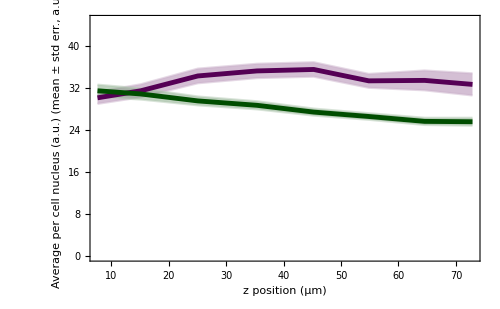

```mathematica
exprAlongZNanogMNG=Show[plotMeanStdLighter[{#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},1,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,45}]
```

### CD1-DapiB-Gata6-YapR-NanogM260315.mdb (Batch 2 in paper)

```mathematica
featuresFNames=FileNames["CD1-DapiB-Gata6G-Yap*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
numEmbryos=Length[featuresFNames]
```

10

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.8054,87.412,1220}

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

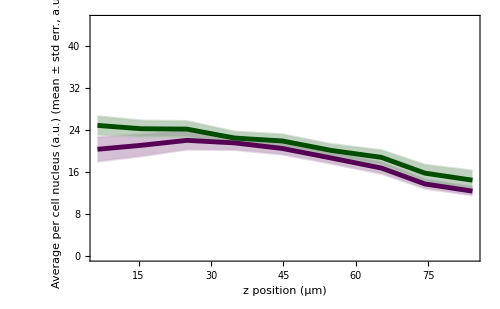

```mathematica
exprAlongZNanogM260315NG=Show[plotMeanStdLighter[{#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},1,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,45}]
```

### CD1-DapiB-Gata6G-ABCr-NanogM (Batch 3 in paper)

```mathematica
featuresFNames=FileNames["CD1-DapiB-Gata6G-ABCr-NanogM*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
Length[featuresFNames]
```

17

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{3.0037,86.406,1314}

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

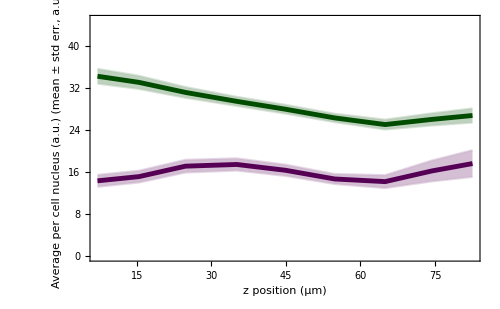

```mathematica
exprAlongZExcelNG=Show[plotMeanStdLighter[{#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},1,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,45}]
```

### CD1-DapiB-Gata6G-TotalR-NanogM.mdb, embryos 14a und 15a (Batch 4 in paper)

```mathematica
featuresFNames=FileNameJoin[{NotebookDirectory[],"EmbryoFeatures",#}]&/@{"CD1-DapiB-Gata6G-TotalRa-NanogM-embryo14a_Features.mx","CD1-DapiB-Gata6G-TotalRa-NanogM-embryo15a_Features.mx"};
```

Embryo 14a and 15a were imaged in a different session:
{{"late", 4.5`, "4.5ncb", "embryo14a", "CD1-DapiB-Gata6G-TotalR-NanogM.mdbA"}, {"late", 4.`, "4.0ncb", "embryo15a", "CD1-DapiB-Gata6G-TotalR-NanogM.mdbA"}}

```mathematica
numEmbryos=Length[featuresFNames]
```

2

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{4.2161,64.502,223}

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

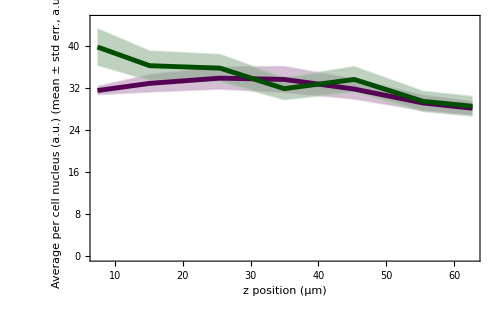

```mathematica
exprAlongZNanogMNG=Show[plotMeanStdLighter[{#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},1,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,45}]
```

## Rescaling because of squeezing when mounting the embryos

separating embryos in early/mid and late 
assume that early and mid blastocysts are spherical, calculate the main axes of these embryos and how much they deviate from spherical, for late embryos use the median rescaling factor

```mathematica
upperBoundCellNumber=91
```

91

```mathematica
rescale[fNamesAll_,upperBoundCellNumber_:upperBoundCellNumber]:=Block[{factorsForRescaling,nucleiFeatures,replace,res},
factorsForRescaling=Median[Cases[(nucleiFeatures="NucleiFeatures"/.Import[#];If[Length[nucleiFeatures]<upperBoundCellNumber,
(2*#[[2,1,2]])/#[[2,1,1]]&@Reap[rescaleCoordSphere["Centroid"/.nucleiFeatures]],
"no rescaling"
])&/@fNamesAll,_List]];
(nucleiFeatures="NucleiFeatures"/.Import[#];
If[Length[nucleiFeatures]<upperBoundCellNumber,
(replace="Centroid"->#&/@rescaleCoordSphere["Centroid"/.nucleiFeatures];
res="NucleiFeatures"->Table[ReplaceAll[nucleiFeatures[[i]],Rule["Centroid",{_,_,_}]->replace[[i]]],{i,1,Length[nucleiFeatures]}];
Export[(StringDrop[#,-3]<>"Rescaled.mx"),res]),
(replace="Centroid"->#&/@rescaleCoordScale["Centroid"/.nucleiFeatures,factorsForRescaling];
res="NucleiFeatures"->Table[ReplaceAll[nucleiFeatures[[i]],Rule["Centroid",{_,_,_}]->replace[[i]]],{i,1,Length[nucleiFeatures]}];
Export[(StringDrop[#,-3]<>"Rescaled.mx"),res])
])&/@fNamesAll
]
```

### CD1-DapiB-Gata6G-TotalR-NanogM.mdb

#### Rescaling

```mathematica
fNamesAll=FileNames["CD1-DapiB-Gata6G-TotalR*_Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll]
```

{C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo11_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo14a_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo15a_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo18b_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo20b_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo21b_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo22b_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo10_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo1_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo2_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo3_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo4_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo5_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo6_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo7_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo8_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo9_FeaturesRescaled.mx}

#### Removing dead cells

according to manual inspection

```mathematica
fNamesRescaled=FileNames["CD1-DapiB-Gata6G-TotalR*_FeaturesRescaled.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

embryo11

```mathematica
dataEmbryo11=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo11"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryo11,"CellID"->105][[1,1;;3]],Position[dataEmbryo11,"CellID"->137][[1,1;;3]]}
```

{{2,101,3},{2,133,3}}

```mathematica
new=Delete[dataEmbryo11,pos[[All,1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{180,16}

```mathematica
Dimensions[dataEmbryo11[[2]]]
```

{182,16}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo11"~~___]][[1]],new]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo11_FeaturesRescaled.mx

embryo6

```mathematica
dataEmbryo6=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo6"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryo6,"CellID"->9][[1,1;;3]]}
```

{{2,9,3}}

```mathematica
new=Delete[dataEmbryo6,pos[[All,1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{121,16}

```mathematica
Dimensions[dataEmbryo6[[2]]]
```

{122,16}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo6"~~___]][[1]],new]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo6_FeaturesRescaled.mx

embryo14a

```mathematica
dataEmbryo14a=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo14a"~~___]][[1]]];
```

```mathematica
pos=Position[dataEmbryo14a,"CellID"->39][[1,1;;3]]
```

{2,39,3}

```mathematica
new=Delete[dataEmbryo14a,pos[[1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{137,16}

```mathematica
Dimensions[dataEmbryo14a[[2]]]
```

{138,16}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo14a"~~___]][[1]],new]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo14a_FeaturesRescaled.mx

### CD1-DapiB-Gata6-YapR-NanogM260315.mdb

#### Rescaling

```mathematica
fNamesAll=FileNames["CD1-DapiB-Gata6G-Yap*_Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll]
```

{C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogM1_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo12_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo13_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo14_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo15_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo2_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo3_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo4_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo5_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo7_FeaturesRescaled.mx}

#### Removing dead cells

according to manual inspection

```mathematica
fNamesRescaled=FileNames["CD1-DapiB-Gata6G-Yap*_FeaturesRescaled.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

embryo3

```mathematica
dataEmbryo3=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo3"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryo3,"CellID"->113][[1,1;;3]]}
```

{{2,85,3}}

```mathematica
new=Delete[dataEmbryo3,pos[[All,1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{223,16}

```mathematica
Dimensions[dataEmbryo3[[2]]]
```

{224,16}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo3"~~___]][[1]],new]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo3_FeaturesRescaled.mx

### CD1-DapiB-Gata6G-ABCr-NanogM

#### Rescaling

```mathematica
fNamesAll=FileNames["CD1-DapiB-Gata6G-ABCr-NanogM*_Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll]
```

{C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoA_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoC_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoF_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoG_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoH_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoI_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoM_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoN_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoO_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoP_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoQ_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoR_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoS_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoT_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoU_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoV_FeaturesRescaled.mx,C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoW_FeaturesRescaled.mx}

#### Removing dead cells

according to manual inspection

```mathematica
fNamesRescaled=FileNames["CD1-DapiB-Gata6G-ABCr-NanogM*_FeaturesRescaled.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

embryoN

```mathematica
dataEmbryoN=Import[Flatten[StringCases[fNamesRescaled,___~~"embryoN"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryoN,"CellID"->19][[1,1;;3]],Position[dataEmbryoN,"CellID"->70][[1,1;;3]]}
```

{{2,19,3},{2,69,3}}

```mathematica
new=Delete[dataEmbryoN,pos[[All,1;;2]]];
```

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryoN"~~___]][[1]],new]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoN_FeaturesRescaled.mx

embryoV

```mathematica
dataEmbryoV=Import[Flatten[StringCases[fNamesRescaled,___~~"embryoV"~~___]][[1]]];
```

```mathematica
pos=Position[dataEmbryoV,"CellID"->145][[1,1;;3]]
```

{2,145,3}

```mathematica
new=Delete[dataEmbryoV,pos[[1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{156,16}

```mathematica
Dimensions[dataEmbryoV[[2]]]
```

{157,16}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryoV"~~___]][[1]],new]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoV_FeaturesRescaled.mx

## Postprocessing

we use the postprocessin gmethod from Schmitz et al. Scientific Reports 2017
we use the rescaled positions for the nuclei of the embryos
for these we calculate the DCG and PCG with a cut off of 30 µm and the corresponding features
the alpha shape is also calculated but outliers are not removed because we set “OutlierDistanceThreshold” tp 10^6 µm

```mathematica
postProcessingPipelinePositions[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}],"*Rescaled.mx","OutlierDistanceThreshold"->10^6,"EdgeDistanceThreshold"->30,"IncludeSubfolders"->False]
```

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoA_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoC_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoF_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoG_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoH_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoI_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoM_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoN_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoO_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoP_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoQ_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoR_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoS_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoT_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoU_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoV_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-ABCr-NanogM-embryoW_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo11_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo14a_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo15a_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo18b_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo20b_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo21b_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalRa-NanogM-embryo22b_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo10_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo1_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo2_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo3_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo4_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo5_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo6_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo7_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo8_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-TotalR-NanogM-embryo9_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogM1_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo12_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo13_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo14_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-Yapr-NanogMembryo15_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo2_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo3_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo4_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo5_FeaturesRescaled.mx

dataset: C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\CD1-DapiB-Gata6G-YapR-NanogMembryo7_FeaturesRescaled.mx

## Aligning the data sets, population thresholds for NANOG and GATA6

four different batches for imaging

### CD1-DapiB-Gata6G-TotalR-NanogM.mdb (Batch 1 in paper)

```mathematica
expLabel="Batch1";
```

```mathematica
finalFNamesRescaledBatch1=FileNames["CD1-DapiB-Gata6G-TotalR*_FeaturesRescaled_Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

Embryo 14a and 15a were imaged in a different session:
{{"late", 4.5`, "4.5ncb", "embryo14a", "CD1-DapiB-Gata6G-TotalR-NanogM.mdbA"}, {"late", 4.`, "4.0ncb", "embryo15a", "CD1-DapiB-Gata6G-TotalR-NanogM.mdbA"}}

```mathematica
finalFNamesRescaledBatch1=Drop[finalFNamesRescaledBatch1,{2,3}];
```

```mathematica
valuesLabeledBatch1=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-Avg","Gata6-Avg"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch1;
```

### CD1-DapiB-Gata6-YapR-NanogM260315.mdb (Batch 2 in paper)

```mathematica
expLabel="Batch2";
```

```mathematica
finalFNamesRescaledBatch2=FileNames["CD1-DapiB-Gata6G-Yap*_FeaturesRescaled_Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch2=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-Avg","Gata6-Avg"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch2;
```

### CD1-DapiB-Gata6G-ABCr-NanogM (Batch 3 in paper)

```mathematica
expLabel="Batch3";
```

```mathematica
finalFNamesRescaledBatch3=FileNames["CD1-DapiB-Gata6G-ABCr-NanogM*_FeaturesRescaled_Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch3=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-Avg","Gata6-Avg"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch3;
```

### CD1-DapiB-Gata6G-TotalR-NanogM.mdb, embryos 14a und 15a (Batch 4 in paper)

```mathematica
expLabel="Batch4";
```

```mathematica
finalFNamesRescaledBatch4=FileNameJoin[{NotebookDirectory[],"EmbryoFeatures",#}]&/@{"CD1-DapiB-Gata6G-TotalRa-NanogM-embryo14a_FeaturesRescaled_Final.mx","CD1-DapiB-Gata6G-TotalRa-NanogM-embryo15a_FeaturesRescaled_Final.mx"};
```

```mathematica
valuesLabeledBatch4=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-Avg","Gata6-Avg"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch4;
```

### Collecting the data

```mathematica
experiments=MapThread[Rule,{{"Batch1","Batch2","Batch3","Batch4"},{1,2,3,4}}]
```

{Batch1→1,Batch2→2,Batch3→3,Batch4→4}

```mathematica
valuesLabeled=Join[valuesLabeledBatch1,valuesLabeledBatch2,valuesLabeledBatch3,valuesLabeledBatch4];
```

```mathematica
finalFNamesRescaled=Join[finalFNamesRescaledBatch1,finalFNamesRescaledBatch2,finalFNamesRescaledBatch3,finalFNamesRescaledBatch4];
```

```mathematica
valuesAllLabeled=Flatten[valuesLabeled,1];
```

```mathematica
valuesAllLabeledICM=Select[valuesAllLabeled,#[[2]]≠"TE"&];
```

```mathematica
valuesLabeledICMByStage={Select[valuesAllLabeledICM,#[[1,3]]==3.5&],Select[valuesAllLabeledICM,#[[1,3]]==4.0&],Select[valuesAllLabeledICM,#[[1,3]]==4.5&]};
```

### Setting population thresholds

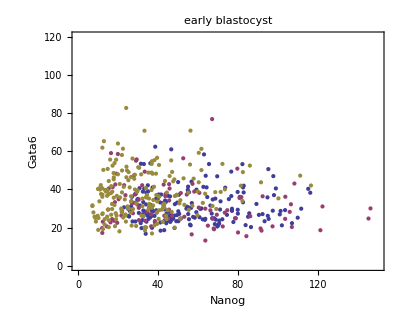
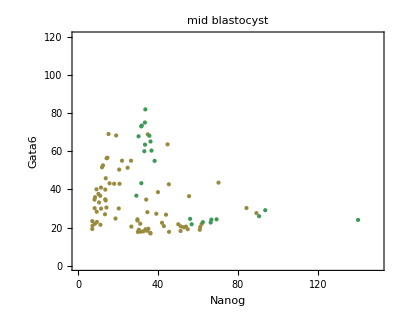
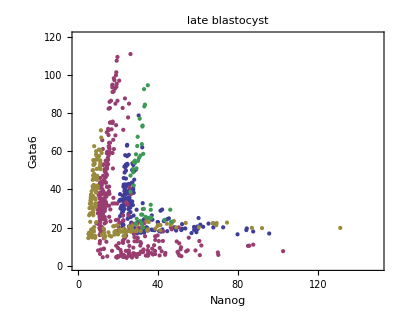
-Graphics--Graphics--Graphics-ICM cells

```mathematica
Labeled[
Row[Table[Show[Graphics[{ColorData[1][#[[1,1]]/.experiments],Point[#[[-2;;-1]]]}&/@valuesLabeledICMByStage[[i]],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}](*,Graphics[{Red,Dashed,Line[{{0,25},{150,25}}],Line[{{40,0},{40,120}}]}]*)],{i,1,3}],"      "],{Style[#,FontFamily->"Helvetica"]&@"ICM cells",SwatchLegend[ColorData[1][#]&/@{1,2,3,4},experiments[[All,1]]]},{Top,Bottom}]
```

#### Set thresholds manually

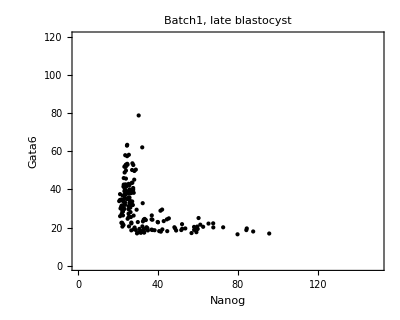
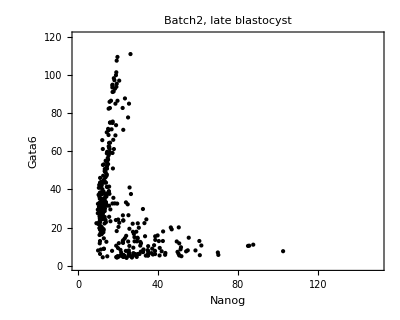
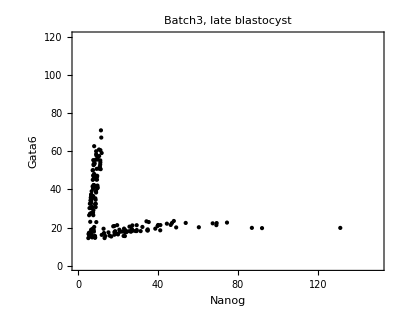
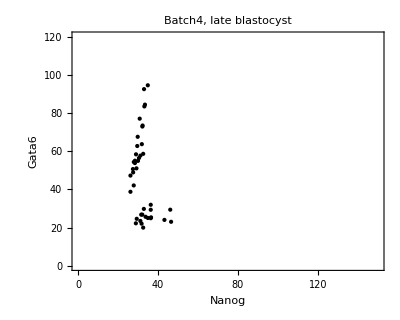

```mathematica
Table[Graphics[Point[#[[-2;;-1]]]&/@Select[valuesLabeledICMByStage[[3]],#[[1,1]]==experiments[[i,1]]&],ImageSize->400,PlotLabel->(experiments[[i,1]]<>",\nlate blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],{i,1,4}]
```

```mathematica
gata6LineIni={29.458,29.738,24.133,29.383}
```

{29.458,29.738,24.133,29.383}

```mathematica
nanogLineIni={32.349,26.478,11.824,38.306}
```

{32.349,26.478,11.824,38.306}

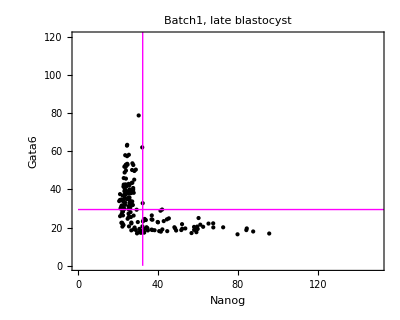
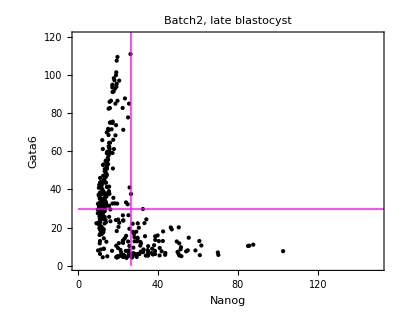
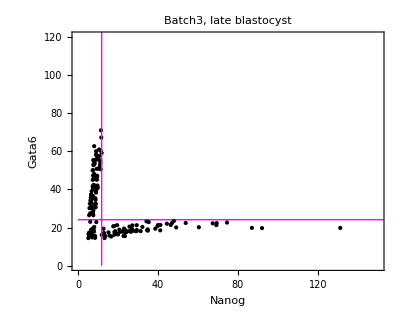
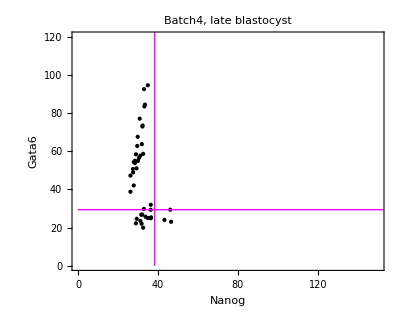

```mathematica
Table[Graphics[{Point[#[[-2;;-1]]]&/@Select[valuesLabeledICMByStage[[3]],#[[1,1]]==experiments[[i,1]]&],Magenta,Line[{{0,gata6LineIni[[i]]},{200,gata6LineIni[[i]]}}],Line[{{nanogLineIni[[i]],0},{nanogLineIni[[i]],150.}}]},ImageSize->400,PlotLabel->(experiments[[i,1]]<>",\nlate blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],{i,1,4}]
```

#### Aligning all data sets

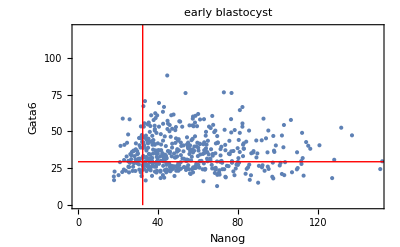
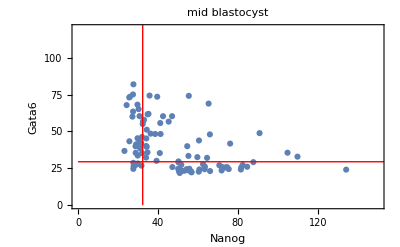
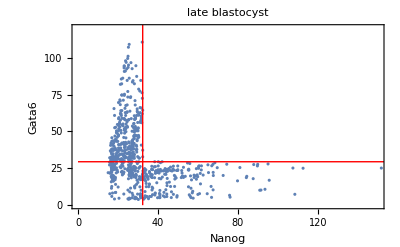

```mathematica
Table[Show[ListPlot[Flatten[Table[#[[-2;;-1]]+{nanogLineIni[[1]]-nanogLineIni[[i]],gata6LineIni[[1]]-gata6LineIni[[i]]}&/@Select[valuesLabeledICMByStage[[j]],#[[1,1]]==experiments[[i,1]]&],{i,1,4}],1],PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],Graphics[{Red,Line[{{0,gata6LineIni[[1]]},{200,gata6LineIni[[1]]}}],Line[{{nanogLineIni[[1]],0},{nanogLineIni[[1]],150.}}]}],ImageSize->400,PlotLabel->({"early","mid","late"}[[j]]<>" blastocyst")],{j,1,3}]
```

#### Determining populations

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNamesRescaled;
```

```mathematica
nucleiFeatShifted=Table[Join[#,{"Nanog-AvgShifted"->shiftValue[valuesLabeled[[i,1,1,1]],"Nanog-Avg",nanogLineIni,experiments],"Gata6-AvgShifted"->shiftValue[valuesLabeled[[i,1,1,1]],"Gata6-Avg",gata6LineIni,experiments]}/.#]&/@nucleiFeatures[[i]],{i,1,Length[nucleiFeatures]}];
```

```mathematica
cellValues=Table[{valuesLabeled[[i,1,1]],Join[#,{"Quadrant"->Switch[{"Nanog-AvgShifted","Gata6-AvgShifted"}/.#,{val1_,val2_}/;val1<=nanogLineIni[[1]]&&val2>gata6LineIni[[1]],"N-G+",{val1_,val2_}/;val1>nanogLineIni[[1]]&&val2>gata6LineIni[[1]],"N+G+",{val1_,val2_}/;val1>nanogLineIni[[1]]&&val2<=gata6LineIni[[1]],"N+G-",{val1_,val2_}/;val1<=nanogLineIni[[1]]&&val2<=gata6LineIni[[1]],"N-G-"]}]&/@nucleiFeatShifted[[i]]},{i,1,Length[nucleiFeatShifted]}];
```

#### Export preprocessed data

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}];
```

```mathematica
Table[Export[FileNameJoin[{outputDir,StringDelete[FileBaseName[finalFNamesRescaled[[i]]],"_FeaturesRescaled"]<>"Data.mx"}],{"NucleiFeatures"->cellValues[[i,2]],"GlobalFeatures"->("GlobalFeatures"/.Import[finalFNamesRescaled[[i]]]),"Staging"->cellValues[[i,1]]}],{i,1,Length[finalFNamesRescaled]}];
```

## Number of neighbours vs distances of ICM cells to ICM centroid (Fig 1 and Fig S3 A)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
cellValues=Transpose[{staging,nucleiFeatures}];
```

```mathematica
cellValuesICM={#[[1]],Select[#[[2]],("TE/ICM"/.#)!="TE"&]}&/@cellValues;
```

```mathematica
posNumNeigh={#[[1,3]],{"Centroid","DCGNeighborCount","Quadrant"}/.#[[2]]}&/@cellValuesICM;
```

#### All ICM cells (Fig 1 C)

```mathematica
distNumNeighByStages=Table[Select[Table[{posNumNeigh[[i,1]],{EuclideanDistance[#[[1]],Mean[#[[All,1]]]&@posNumNeigh[[i,2]]],#[[2]],#[[3]]}&/@posNumNeigh[[i,2]]},{i,1,Length[posNumNeigh]}],#[[1]]==j&],{j,{3.5,4.0,4.5}}];
```

```mathematica
avgRadius=Median[Flatten[Table[Max[#[[All,1]]]&/@distNumNeighByStages[[i,All,2]],{i,1,3}]]]
```

34.3987

```mathematica
avgDistNeighByStages=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[#[[1;;2]]&/@Flatten[distNumNeighByStages[[i,All,2]],1],{0,65,5},{0,10^6,10^6}],1],Length[#]>0&]),{i,1,3}];
```

use only those for more than one cell, hence std dev is not 0

```mathematica
avgDistNeighByStagesNoS0=Select[#,#[[3]]!=0&]&/@avgDistNeighByStages;
```

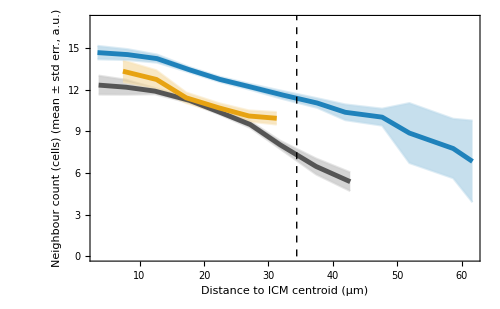

```mathematica
plotDistCentNanog=Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistNeighByStagesNoS0,#[[All,2;;3]]&/@avgDistNeighByStagesNoS0,1,"Distance to ICM centroid (µm)","Neighbour count (cells)\n(mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,17},ImageSize->500]
```

#### By population (Fig S3 A)

```mathematica
calcDistNeighPyPopulation[posNumNeigh_,population_]:=Block[{posNumNeighPop,distNumNeighByStagesPop,avgDistNeighByStagesPop},
posNumNeighPop=Select[Table[{posNumNeigh[[i,1]],Select[posNumNeigh[[i,2]],#[[-1]]==population&]},{i,1,Length[posNumNeigh]}],Length[#[[2]]]>0&];
distNumNeighByStagesPop=Select[Table[Select[Table[{posNumNeighPop[[i,1]],{EuclideanDistance[#[[1]],Mean[#[[All,1]]]&@posNumNeighPop[[i,2]]],#[[2]],#[[3]]}&/@posNumNeighPop[[i,2]]},{i,1,Length[posNumNeighPop]}],#[[1]]==j&],{j,{3.5,4.0,4.5}}],Length[#]>0&];
avgDistNeighByStagesPop=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[#[[1;;2]]&/@Flatten[distNumNeighByStagesPop[[i,All,2]],1],{0,65,5},{0,10^6,10^6}],1],Length[#]>0&]),{i,1,Length[distNumNeighByStagesPop]}];
(*use only those for more than one cell,hence std dev is not 0*)
Select[#,#[[3]]!=0&]&/@avgDistNeighByStagesPop
]
```

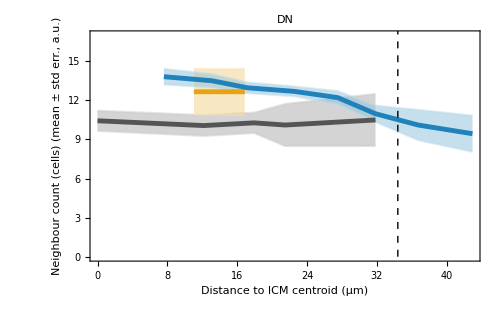

```mathematica
plotDistCentDN=(avgDistNeighByStagesPopNoS0=(calcDistNeighPyPopulation[posNumNeigh,"N-G-"]);Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistNeighByStagesPopNoS0,#[[All,2;;3]]&/@avgDistNeighByStagesPopNoS0,1,"Distance to ICM centroid (µm)","Neighbour count (cells)\n(mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,17},ImageSize->500,PlotLabel->Style["DN",Black,FontFamily->fontOption,14]])
```

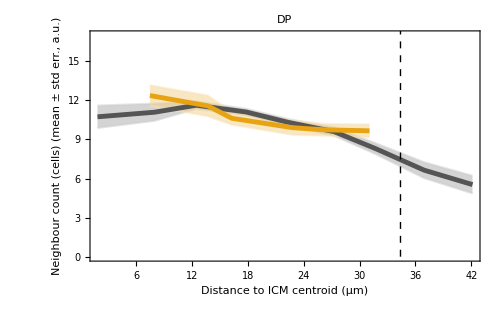

```mathematica
plotDistCentDP=(avgDistNeighByStagesPopNoS0=(calcDistNeighPyPopulation[posNumNeigh,"N+G+"]);Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistNeighByStagesPopNoS0,#[[All,2;;3]]&/@avgDistNeighByStagesPopNoS0,1,"Distance to ICM centroid (µm)","Neighbour count (cells)\n(mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,17},ImageSize->500,PlotLabel->Style["DP",Black,FontFamily->fontOption,14]])
```

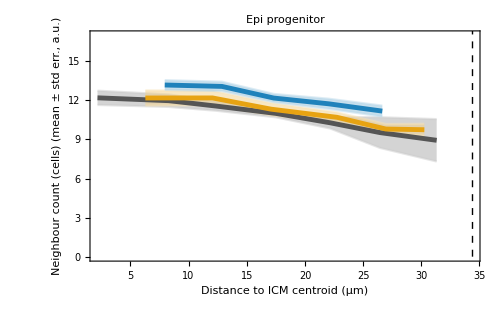

```mathematica
plotDistCentNpGm=(avgDistNeighByStagesPopNoS0=(calcDistNeighPyPopulation[posNumNeigh,"N+G-"]);Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistNeighByStagesPopNoS0,#[[All,2;;3]]&/@avgDistNeighByStagesPopNoS0,1,"Distance to ICM centroid (µm)","Neighbour count (cells)\n(mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,17},ImageSize->500,PlotLabel->Style["Epi progenitor",Black,FontFamily->fontOption,14]])
```

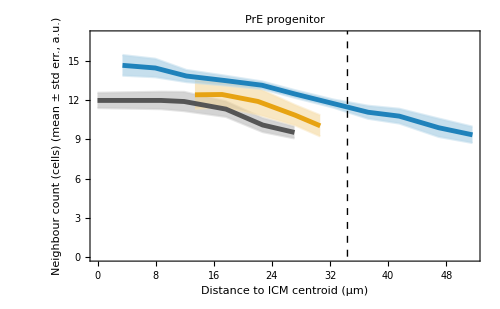

```mathematica
plotDistCentNmGp=(avgDistNeighByStagesPopNoS0=(calcDistNeighPyPopulation[posNumNeigh,"N-G+"]);Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistNeighByStagesPopNoS0,#[[All,2;;3]]&/@avgDistNeighByStagesPopNoS0,1,"Distance to ICM centroid (µm)","Neighbour count (cells)\n(mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,17},ImageSize->500,PlotLabel->Style["PrE progenitor",Black,FontFamily->fontOption,14]])
```

## Distribution population of neighbours (Fig 2)

```mathematica
finalFNames=FileNames["*_FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=ParallelMap[("NucleiFeatures"/.Import[#])&,finalFNames];
```

```mathematica
staging=ParallelMap[("Staging"/.Import[#])&,finalFNames];
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

```mathematica
AbsoluteTiming[gata6Gata6CompPopRaw=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];]
```

{11.0091,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures","gata6Gata6CompPop.mx"}],gata6Gata6CompPopRaw]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\EmbryoFeatures\gata6Gata6CompPop.mx

```mathematica
gata6Gata6CompPopRaw=Import[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures","gata6Gata6CompPop.mx"}]];
```

```mathematica
gata6Gata6CompPop=gata6Gata6CompPopRaw/.{a_,"TE",_}->{a,"TE","TE"};
```

```mathematica
gata6Gata6CompByStages={Select[gata6Gata6CompPop,#[[1,3]]==3.5&],Select[gata6Gata6CompPop,#[[1,3]]==4.0&],Select[gata6Gata6CompPop,#[[1,3]]==4.5&]};
```

consider only ICM cells

```mathematica
gata6Gata6CompByStagesICM=Table[{#[[1]],Select[#[[2]],#[[1,1]]!="TE"&]}&/@gata6Gata6CompByStages[[i]],{i,1,3}];
```

#### consider all neighbours (ICM and TE)

```mathematica
propNeighboursOfPrEICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-1]],pop]/Length[#],0]&/@Select[Flatten[gata6Gata6CompByStagesICM[[i,All,2]],1],#[[1,2]]=="N-G+"&][[All,2]]},{pop,{"TE","N-G-","N+G+","N+G-","N-G+"}}],{i,1,3}];
```

```mathematica
propNeighboursOfDPICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-1]],pop]/Length[#],0]&/@Select[Flatten[gata6Gata6CompByStagesICM[[i,All,2]],1],#[[1,2]]=="N+G+"&][[All,2]]},{pop,{"TE","N-G-","N+G+","N+G-","N-G+"}}],{i,1,3}];
```

```mathematica
propNeighboursOfDNICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-1]],pop]/Length[#],0]&/@Select[Flatten[gata6Gata6CompByStagesICM[[i,All,2]],1],#[[1,2]]=="N-G-"&][[All,2]]},{pop,{"TE","N-G-","N+G+","N+G-","N-G+"}}],{i,1,3}];
```

```mathematica
propNeighboursOfEpiICM=Table[Table[{pop,If[Length[#]>0,N@Count[#[[All,-1]],pop]/Length[#],0]&/@Select[Flatten[gata6Gata6CompByStagesICM[[i,All,2]],1],#[[1,2]]=="N+G-"&][[All,2]]},{pop,{"TE","N-G-","N+G+","N+G-","N-G+"}}],{i,1,3}];
```

ignore warning - occurs because there are no DP cells in late embryos

Transpose::nmtx: The first two levels of {} cannot be transposed.

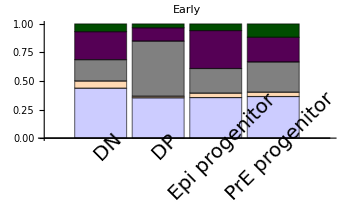
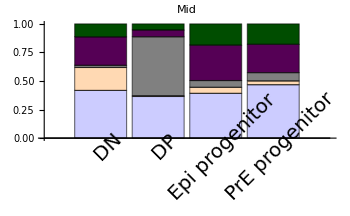
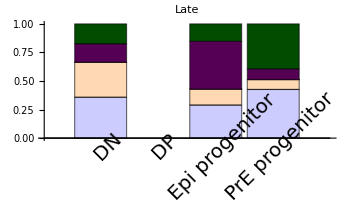

```mathematica
neighbourTypePopulationExpICM=Labeled[Row[Table[BarChart[{
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfDNICM[[i,All,2]]],Total[#]>0&]],
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfDPICM[[i,All,2]]],Total[#]>0&]],
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfEpiICM[[i,All,2]]],Total[#]>0&]],
Mean[#]&/@Transpose[Select[Transpose[propNeighboursOfPrEICM[[i,All,2]]],Total[#]>0&]]},ChartLayout->"Stacked",ChartStyle->{Lighter[Blue,0.8],Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},AxesStyle->Directive[Black,FontFamily->"Arial",20],ChartLabels->{Style[Rotate[#,45°],Black,FontFamily->"Arial",20]&/@{"DN","DP","Epi progenitor","PrE progenitor"},None},PlotLabel->(Style[#,Black,FontFamily->"Arial",20]&@(({"Early","Mid","Late"}[[i]]))),ImageSize->350],{i,1,3}]],SwatchLegend[{Lighter[Blue,0.8],Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},Style[#,Black,FontFamily->"Arial",20]&/@{"TE","DN","DP","Epi progenitor","PrE progenitor"},LegendLayout->"Row"]]
```

## Correlations between neighbouring cells in ICM (Fig 3 and Fig S5; Fig 5, Fig S8 C-F, Fig 7 B and Fig 8 analogous)

for each stage, calculate for each cell the Median expression level of its neighbours
all neighbours are included independent of whether they are ICM or TE

Separate the results by populations

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

```mathematica
gata6Gata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogNanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
gata6NanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogGata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogValNeighByStages={Select[nanogNanogComp,#[[1,3]]==3.5&],Select[nanogNanogComp,#[[1,3]]==4.0&],Select[nanogNanogComp,#[[1,3]]==4.5&]};
```

```mathematica
gata6ValNeighByStages={Select[gata6Gata6Comp,#[[1,3]]==3.5&],Select[gata6Gata6Comp,#[[1,3]]==4.0&],Select[gata6Gata6Comp,#[[1,3]]==4.5&]};
```

```mathematica
nanogValGata6NeighByStages={Select[nanogGata6Comp,#[[1,3]]==3.5&],Select[nanogGata6Comp,#[[1,3]]==4.0&],Select[nanogGata6Comp,#[[1,3]]==4.5&]};
```

```mathematica
gata6ValNanogNeighByStages={Select[gata6NanogComp,#[[1,3]]==3.5&],Select[gata6NanogComp,#[[1,3]]==4.0&],Select[gata6NanogComp,#[[1,3]]==4.5&]};
```

### NANOG cell, NANOG neighbours

```mathematica
plotDataDPEarly=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[1,All,2]],1],(#[[2]]=="N+G+")&&(#[[1]]≠"TE")&];
```

```mathematica
plotDataNpGmEarly=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[1,All,2]],1],(#[[2]]=="N+G-")&&(#[[1]]≠"TE")&];
```

```mathematica
plotDataNpGmLate=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[3,All,2]],1],(#[[2]]=="N+G-")&&(#[[1]]≠"TE")&];
```

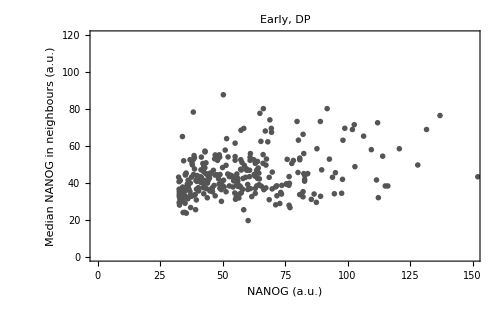

```mathematica
nanogNanogEarlyDP=Graphics[{colour2[1],PointSize->0.008,Point/@plotDataDPEarly[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"NANOG (a.u.)","Median NANOG in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Early, DP",14,Black,FontFamily->fontOption]]
```

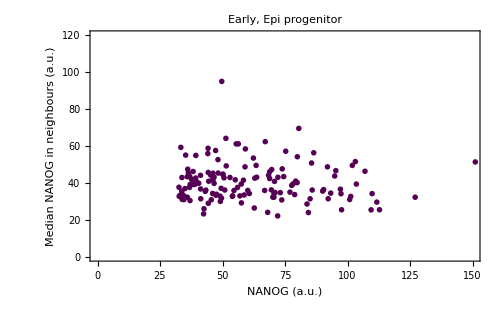

```mathematica
nanogNanogEarlyNpGm=Graphics[{colour2[2],PointSize->0.008,Point/@plotDataNpGmEarly[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"NANOG (a.u.)","Median NANOG in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Early, Epi progenitor",14,Black,FontFamily->fontOption]]
```

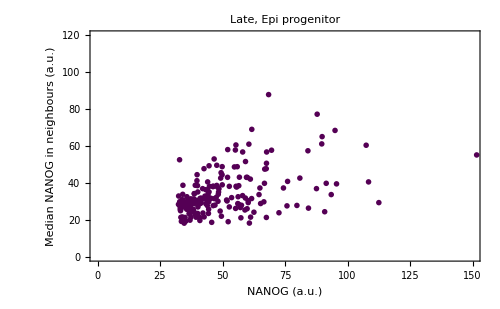

```mathematica
nanogNanogLateNpGm=Graphics[{colour2[2],PointSize->0.008,Point/@plotDataNpGmLate[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"NANOG (a.u.)","Median NANOG in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Late, Epi progenitor",14,Black,FontFamily->fontOption]]
```

```mathematica
exportListNanogEarly=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Early blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[1,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[1,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[1,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[1,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListNanogMid=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Mid blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[2,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[2,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[2,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[2,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListNanogLate=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Late blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[3,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[3,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[3,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValNeighByStages[[3,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

### GATA6 cell, GATA6 neighbours

```mathematica
plotDataDPEarly=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[1,All,2]],1],(#[[2]]=="N+G+")&&(#[[1]]≠"TE")&];
```

```mathematica
plotDataNmGpLate=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[3,All,2]],1],(#[[2]]=="N-G+")&&(#[[1]]≠"TE")&];
```

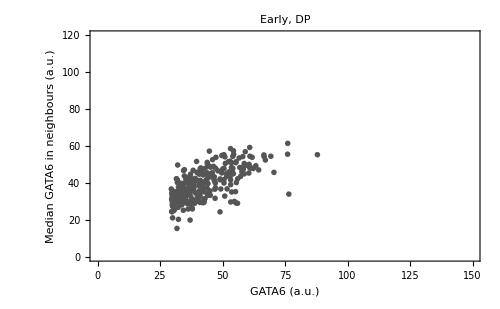

```mathematica
gata6Gata6EarlyDP=Graphics[{colour2[1],PointSize->0.008,Point/@plotDataDPEarly[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"GATA6 (a.u.)","Median GATA6 in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Early, DP",14,Black,FontFamily->fontOption]]
```

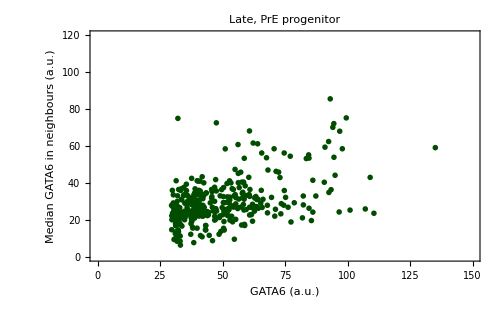

```mathematica
gata6Gata6LateNmGp=Graphics[{colour2[3],PointSize->0.008,Point/@plotDataNmGpLate[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"GATA6 (a.u.)","Median GATA6 in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Late, PrE progenitor",14,Black,FontFamily->fontOption]]
```

```mathematica
exportListGata6Early=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Early blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[1,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[1,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[1,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[1,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListGata6Mid=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Mid blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[2,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[2,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[2,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[2,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListGata6Late=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Late blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[3,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[3,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[3,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNeighByStages[[3,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

### GATA6 cell, NANOG neighbours

```mathematica
plotDataDPEarly=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[1,All,2]],1],(#[[2]]=="N+G+")&&(#[[1]]≠"TE")&];
```

```mathematica
plotDataNmGpLate=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[3,All,2]],1],(#[[2]]=="N-G+")&&(#[[1]]≠"TE")&];
```

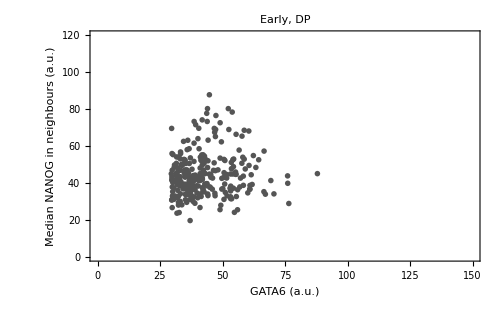

```mathematica
gata6NanogEarlyDP=Graphics[{colour2[1],PointSize->0.008,Point/@plotDataDPEarly[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"GATA6 (a.u.)","Median NANOG in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Early, DP",14,Black,FontFamily->fontOption]]
```

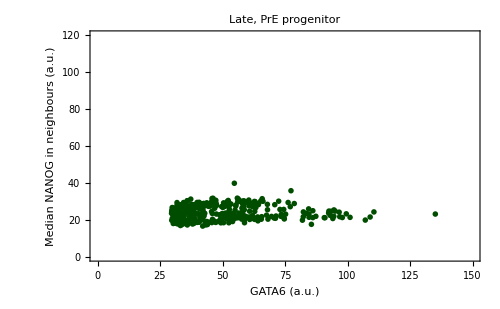

```mathematica
gata6NanogLateNmGp=Graphics[{colour2[3],PointSize->0.008,Point/@plotDataNmGpLate[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"GATA6 (a.u.)","Median NANOG in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Late, PrE progenitor",14,Black,FontFamily->fontOption]]
```

```mathematica
exportListGata6NanogEarly=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Early blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[1,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[1,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[1,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[1,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListGata6NanogMid=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Mid blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[2,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[2,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[2,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[2,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListGata6NanogLate=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Late blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[3,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[3,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[3,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Gata6 in a cell and Nanog of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[gata6ValNanogNeighByStages[[3,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

### NANOG cell, GATA6 neighbours

```mathematica
plotDataDPEarly=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[1,All,2]],1],(#[[2]]=="N+G+")&&(#[[1]]≠"TE")&];
```

```mathematica
plotDataNpGmEarly=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[1,All,2]],1],(#[[2]]=="N+G-")&&(#[[1]]≠"TE")&];
```

```mathematica
plotDataNpGmLate=Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[3,All,2]],1],(#[[2]]=="N+G-")&&(#[[1]]≠"TE")&];
```

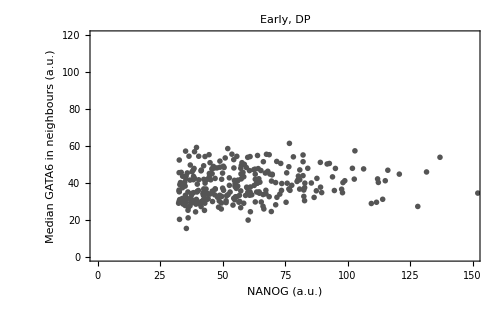

```mathematica
nanogGata6EarlyDP=Graphics[{colour2[1],PointSize->0.008,Point/@plotDataDPEarly[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"NANOG (a.u.)","Median GATA6 in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Early, DP",14,Black,FontFamily->fontOption]]
```

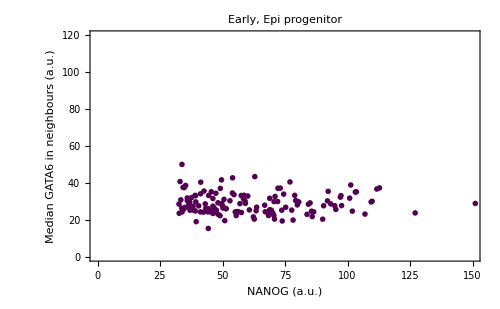

```mathematica
nanogGata6EarlyNpGm=Graphics[{colour2[2],PointSize->0.008,Point/@plotDataNpGmEarly[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"NANOG (a.u.)","Median GATA6 in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Early, Epi progenitor",14,Black,FontFamily->fontOption]]
```

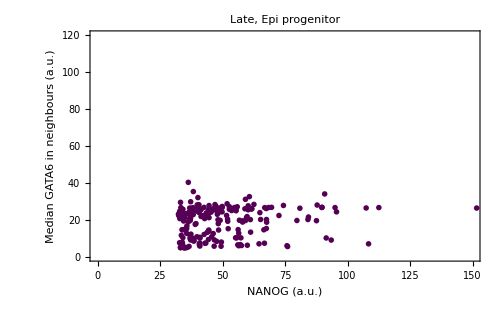

```mathematica
nanogGata6LateNpGm=Graphics[{colour2[2],PointSize->0.008,Point/@plotDataNpGmLate[[All,3;;4]]},PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"NANOG (a.u.)","Median GATA6 in neighbours (a.u.)"},FrameStyle->Directive[14,Black,FontFamily->fontOption],ImageSize->500,AspectRatio->1/GoldenRatio,PlotLabel->Style["Late, Epi progenitor",14,Black,FontFamily->fontOption]]
```

```mathematica
exportListNanogGata6Early=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Early blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[1,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[1,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[1,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[1,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListNanogGata6Mid=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Mid blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[2,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[2,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[2,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[2,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

```mathematica
exportListNanogGata6Late=MapThread[Rule,{{"N-G+","N+G+","N-G-","N+G-"},{Join[{{"Late blastocyst (NCB staging): Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[3,All,2]],1],#[[2]]=="N-G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6+"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[3,All,2]],1],#[[2]]=="N+G+"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog-/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[3,All,2]],1],#[[2]]=="N-G-"&]],
Join[{{"Values neighbourhood analysis", "","","",DateString[]},{"comparison Nanog in a cell and Gata6 of its neighbours, Expression levels aligned by quadrant thresholds, Nanog+/Gata6-"},{"cell type","population","expression level of cell","Median expression level of neighbours"}},Select[{#[[1,1]],#[[1,2]],#[[1,3]],Median[#[[2,All,1]]]}&/@Flatten[nanogValGata6NeighByStages[[3,All,2]],1],#[[2]]=="N+G-"&]]}}];
```

## Expression levels vs number of neighbours of ICM cells (Fig 4 A and B; Fig S8 A and B and Fig S12 A and B analogous)

take all cells of the ICM, count the number of neighbours (include all neighbours ICM and TE)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

#### NANOG (Fig 4 A)

```mathematica
nanogNumNeighbours=Table[{staging[[i]],{"TE/ICM","DCGNeighborCount","Nanog-AvgShifted"}/.nucleiFeatures[[i]]},{i,1,Length[staging]}];
```

```mathematica
nanogNumNeighboursByStages={Select[nanogNumNeighbours,#[[1,3]]==3.5&],Select[nanogNumNeighbours,#[[1,3]]==4.0&],Select[nanogNumNeighbours,#[[1,3]]==4.5&]};
```

```mathematica
nanogNumNeighbByStagesAvgICMAll=Table[SortBy[{#[[1,1]],Mean[#[[All,2]]],If[Length[#]>1,StandardDeviation[#[[All,2]]]/Sqrt[Length[#]],0]}&/@GatherBy[Select[Flatten[nanogNumNeighboursByStages[[i,All,2]],1],#[[1]]≠"TE"&][[All,-2;;-1]],#[[1]]&],#[[1]]&],{i,1,3}];
```

remove those that are only for one cell, i.e. std dev =0

```mathematica
nanogNumNeighbByStagesAvgICMAllNS0=Select[#,#[[3]]≠0&]&/@nanogNumNeighbByStagesAvgICMAll;
```

```mathematica
nanogNumNeighbByStagesAvgICMAllNS0Smooth=smoothedValues[nanogNumNeighbByStagesAvgICMAllNS0,1];
```

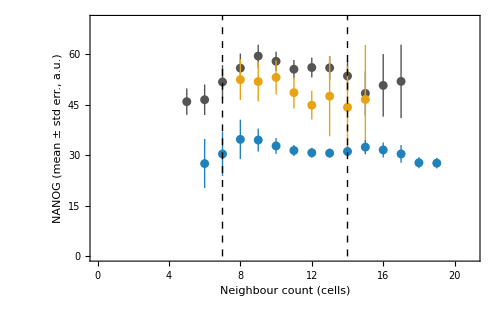

```mathematica
neighNumNPoint=Show[ErrorListPlot[Table[{#[[1;;2]],ErrorBar[#[[3]]]}&/@nanogNumNeighbByStagesAvgICMAllNS0Smooth[[i]],{i,1,3}],PlotStyle->({Thick,colour3[#]}&/@{1,2,3}),PlotRange->{{0,21},{0,70}},AxesOrigin->{0,0},Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{"Neighbour count (cells)","NANOG (mean ± std err., a.u.)"},ImageSize->500,Joined->False],Graphics[{Black,Dashed,Line[{{7,0},{7,75}}],Line[{{14,0},{14,75}}]}]]
```

#### GATA6 (Fig 4 B)

```mathematica
gata6NumNeighbours=Table[{staging[[i]],{"TE/ICM","DCGNeighborCount","Gata6-AvgShifted"}/.nucleiFeatures[[i]]},{i,1,Length[staging]}];
```

```mathematica
gata6NumNeighboursByStages={Select[gata6NumNeighbours,#[[1,3]]==3.5&],Select[gata6NumNeighbours,#[[1,3]]==4.0&],Select[gata6NumNeighbours,#[[1,3]]==4.5&]};
```

```mathematica
gata6NumNeighbByStagesAvgICMAll=Table[SortBy[{#[[1,1]],Mean[#[[All,2]]],If[Length[#]>1,StandardDeviation[#[[All,2]]]/Sqrt[Length[#]],0]}&/@GatherBy[Select[Flatten[gata6NumNeighboursByStages[[i,All,2]],1],#[[1]]≠"TE"&][[All,-2;;-1]],#[[1]]&],#[[1]]&],{i,1,3}];
```

remove those that are only for one cell, i.e. std dev =0

```mathematica
gata6NumNeighbByStagesAvgICMAllNS0=Select[#,#[[3]]≠0&]&/@gata6NumNeighbByStagesAvgICMAll;
```

```mathematica
gata6NumNeighbByStagesAvgICMAllNS0Smooth=smoothedValues[gata6NumNeighbByStagesAvgICMAllNS0,1];
```

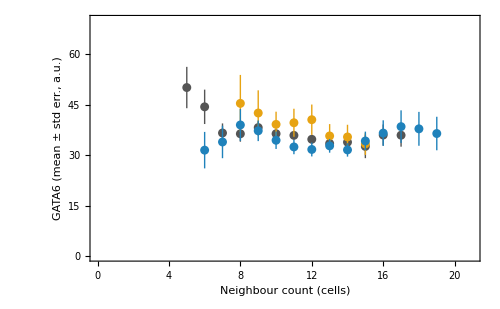

```mathematica
neighNumGPoint=ErrorListPlot[Table[{#[[1;;2]],ErrorBar[#[[3]]]}&/@gata6NumNeighbByStagesAvgICMAllNS0Smooth[[i]],{i,1,3}],PlotStyle->({Thick,colour3[#]}&/@{1,2,3}),PlotRange->{{0,21},{0,70}},AxesOrigin->{0,0},Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{"Neighbour count (cells)","GATA6 (mean ± std err., a.u.)"},ImageSize->500,Joined->False]
```

## Expression levels vs distances of ICM cells to ICM centroid (Fig 4 C and D; Fig S8 G and H, Fig 7 C and Fig S12 C-F analogous)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
cellValues=Transpose[{staging,nucleiFeatures}];
```

```mathematica
cellValuesICM={#[[1]],Select[#[[2]],("TE/ICM"/.#)!="TE"&]}&/@cellValues;
```

```mathematica
posExprICM={#[[1,3]],{"Centroid","Nanog-AvgShifted","Gata6-AvgShifted"}/.#[[2]]}&/@cellValuesICM;
```

calculate distance of cell to ICM centroid

### absolute

```mathematica
distExprICMByStages=Table[Select[Table[{posExprICM[[i,1]],{EuclideanDistance[#[[1]],Mean[#[[All,1]]]&@posExprICM[[i,2]]],#[[2]],#[[3]]}&/@posExprICM[[i,2]]},{i,1,Length[posExprICM]}],#[[1]]==j&],{j,{3.5,4.0,4.5}}];
```

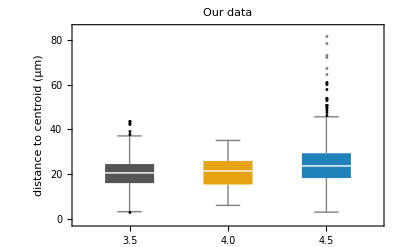

```mathematica
BoxWhiskerChart[Table[Flatten[distExprICMByStages[[i,All,2]],1][[All,1]],{i,1,3}],"Outliers",ChartLabels->{"3.5","4.0","4.5"},FrameLabel->{None,"distance to centroid (µm)",None,None},FrameStyle->Directive[Black,16,FontFamily->"Arial"],ChartStyle->(colour3/@{1,2,3}),PlotLabel->Style["Our data",Black,16,FontFamily->"Arial"]]
```

```mathematica
avgRadius=Median[Flatten[Table[Max[#[[All,1]]]&/@distExprICMByStages[[i,All,2]],{i,1,3}]]]
```

34.3987

```mathematica
avgDistNanogByStages=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[#[[1;;2]]&/@Flatten[distExprICMByStages[[i,All,2]],1],{0,65,5},{0,10^6,10^6}],1],Length[#]>0&]),{i,1,3}];
```

use only those for more than one cell, hence std dev is not 0

```mathematica
avgDistNanogByStagesNoS0=Select[#,#[[3]]!=0&]&/@avgDistNanogByStages;
```

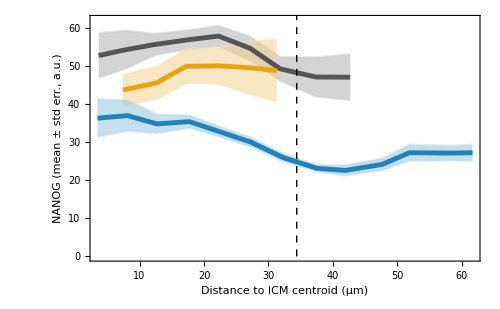

```mathematica
plotDistCentNanog=Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistNanogByStagesNoS0,#[[All,2;;3]]&/@avgDistNanogByStagesNoS0,1,"Distance to ICM centroid (µm)","NANOG (mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,62},ImageSize->500]
```

```mathematica
avgDistGata6ByStages=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[#[[{1,3}]]&/@Flatten[distExprICMByStages[[i,All,2]],1],{0,65,5},{0,10^6,10^6}],1],Length[#]>0&]),{i,1,3}];
```

```mathematica
avgDistGata6ByStagesNoS0=Select[#,#[[3]]!=0&]&/@avgDistGata6ByStages;
```

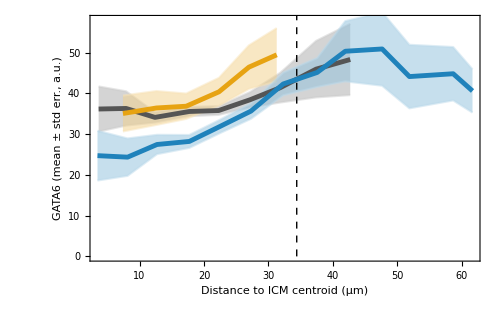

```mathematica
plotDistCentGata6=Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistGata6ByStagesNoS0,#[[All,2;;3]]&/@avgDistGata6ByStagesNoS0,1,"Distance to ICM centroid (µm)","GATA6 (mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,58},ImageSize->500]
```

## For simulation of four cell populations see separate file (Fig 6 and Fig 7 D)

## Raw expression and populations in ICM (Fig S1 and S2)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
Count[staging,#,{2}]&/@{3.5,4.0,4.5}
```

{24,4,16}

```mathematica
Length[finalFNames]
```

44

```mathematica
experiments=MapThread[Rule,{Union[staging[[All,1]]],{1,2,3,4}}]
```

{Batch1→1,Batch2→2,Batch3→3,Batch4→4}

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
nucleiFeaturesICM=Select[#,("TE/ICM"/.#)≠"TE"&]&/@nucleiFeatures;
```

```mathematica
cellValuesICM=Transpose[{staging,nucleiFeaturesICM}];
```

```mathematica
cellValuesICMByStage={Select[cellValuesICM,#[[1,3]]==3.5&],Select[cellValuesICM,#[[1,3]]==4.0&],Select[cellValuesICM,#[[1,3]]==4.5&]};
```

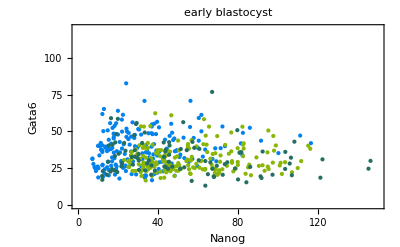
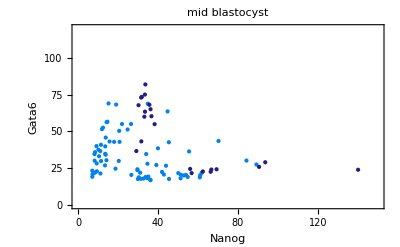
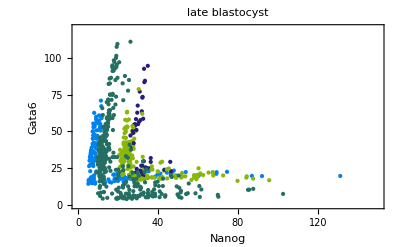
-Graphics--Graphics--Graphics-ICM cells

```mathematica
Labeled[
Row[Table[Show[Graphics[{ColorData[3][3+#[[1,1]]/.experiments],PointSize->0.008,Point/@({"Nanog-Avg","Gata6-Avg"}/.#[[2]])}&/@cellValuesICMByStage[[i]],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"},AspectRatio->1/GoldenRatio]],{i,1,3}],"      "],{Style[#,FontFamily->"Arial"]&@"ICM cells",SwatchLegend[ColorData[3][3+#]&/@{1,2,3,4},{"Batch 1","Batch 2","Batch 3","Batch 4"}]},{Top,Bottom}]
```

### B

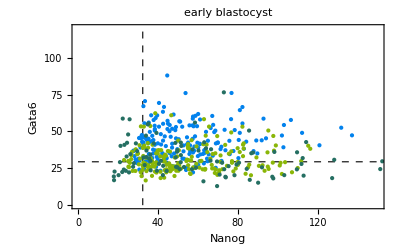
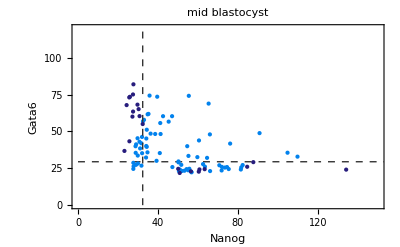
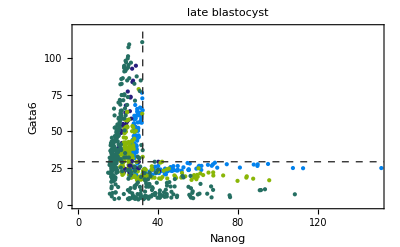
-Graphics--Graphics--Graphics-ICM cells

```mathematica
Labeled[
Row[Table[Show[Graphics[{ColorData[3][3+#[[1,1]]/.experiments],PointSize->0.008,Point/@({"Nanog-AvgShifted","Gata6-AvgShifted"}/.#[[2]])}&/@cellValuesICMByStage[[i]],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"},AspectRatio->1/GoldenRatio],Graphics[{GrayLevel[0.2],Dashed,Line[{{0,gata6LineIni[[1]]},{200,gata6LineIni[[1]]}}],Line[{{nanogLineIni[[1]],0},{nanogLineIni[[1]],150.}}]}]],{i,1,3}],"      "],{Style[#,FontFamily->"Arial"]&@"ICM cells"},{Top,Bottom}]
```

### S2 A

```mathematica
populationsCountICM=Table[{cellValuesICM[[i,1,1]],cellValuesICM[[i,1,2]],cellValuesICM[[i,1,3]],Count["Quadrant"/.cellValuesICM[[i,2]],#]&/@{"N-G-","N+G+","N+G-","N-G+"}},{i,1,Length[cellValuesICM]}];
```

```mathematica
populationsCountByStageICM=Table[Select[populationsCountICM,#[[3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountAllICMByStage=Table[Total@populationsCountByStageICM[[i,All,-1]],{i,1,3}]
```

{{23,280,145,37},{6,34,33,23},{170,0,201,341}}

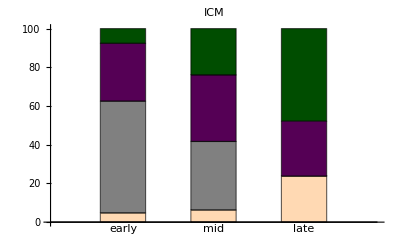

```mathematica
Labeled[BarChart[popCountAllICMByStage,BarSpacing->1,ChartLayout->"Percentile",ImageSize->400,ChartStyle->{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},ChartLabels->{{"early","mid","late"},None},PlotLabel->"ICM"], SwatchLegend[{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},{"DN","DP","Epi progenitor","PrE progenitor"},LegendLayout->"Row"]]
```

## TE populations count (Fig S2) and null model for correlations (Sup. Info)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

### Null model for correlations analysis with TE neighbours from data

#### Underlying data ICM cells

```mathematica
nucleiFeaturesICM=Select[#,("TE/ICM"/.#)≠"TE"&]&/@nucleiFeatures;
```

```mathematica
exprNanogICM=Select[Flatten[{"TE/ICM","Nanog-AvgShifted"}/.nucleiFeaturesICM,1],#[[2]]>0&][[All,2]];
```

```mathematica
Mean[exprNanogICM]
```

42.0196

```mathematica
exprGata6ICM=Select[Flatten[{"TE/ICM","Gata6-AvgShifted"}/.nucleiFeaturesICM,1],#[[2]]>0&][[All,2]];
```

```mathematica
Mean[exprGata6ICM]
```

35.0867

```mathematica
gata6LineIni[[1]]
```

29.458

```mathematica
nanogLineIni[[1]]
```

32.349

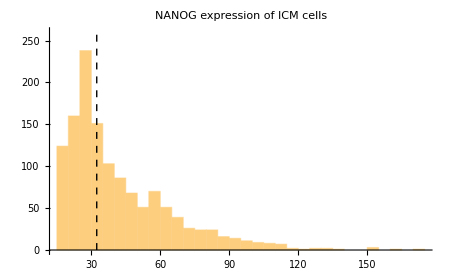
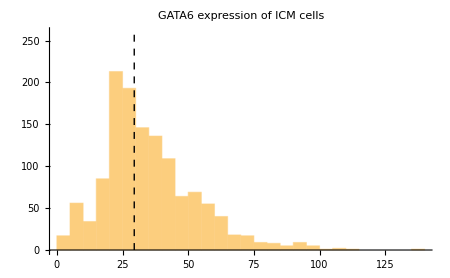

```mathematica
Row[{Show[Histogram[exprNanogICM,PlotLabel->"NANOG expression of ICM cells",ImageSize->450,PlotRange->All],Graphics[{Black,Dashed,Line[{{nanogLineIni[[1]],0},{nanogLineIni[[1]],260}}]}]],Show[Histogram[exprGata6ICM,PlotLabel->"GATA6 expression of ICM cells",PlotRange->All,ImageSize->450],Graphics[{Black,Dashed,Line[{{gata6LineIni[[1]],0},{gata6LineIni[[1]],260}}]}]]},"    "]
```

```mathematica
cellValuesICM=Transpose[{staging,nucleiFeaturesICM}];
```

```mathematica
cellValuesICMByStage={Select[cellValuesICM,#[[1,3]]==3.5&],Select[cellValuesICM,#[[1,3]]==4.0&],Select[cellValuesICM,#[[1,3]]==4.5&]};
```

```mathematica
exprNanogICMByStage=Table[Flatten["Nanog-AvgShifted"/.cellValuesICMByStage[[i,All,2]],1],{i,1,3}];
```

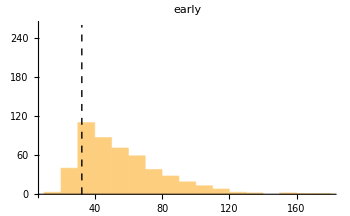
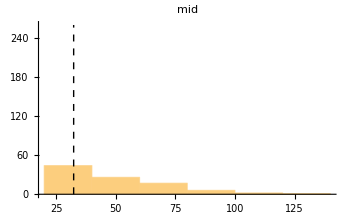
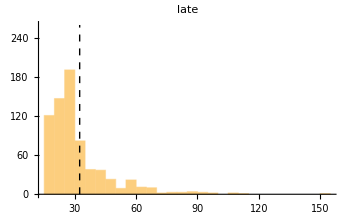
-Graphics--Graphics--Graphics-NANOG expression of ICM cells

```mathematica
Labeled[Row[Table[Show[Histogram[exprNanogICMByStage[[i]],PlotLabel->{"early","mid","late"}[[i]],ImageSize->350,PlotRange->All],Graphics[{Black,Dashed,Line[{{nanogLineIni[[1]],0},{nanogLineIni[[1]],260}}]}]],{i,1,3}]],Style["NANOG expression of ICM cells",FontFamily->fontOption,14],Top]
```

```mathematica
exprGata6ICMByStage=Table[Flatten["Gata6-AvgShifted"/.cellValuesICMByStage[[i,All,2]],1],{i,1,3}];
```

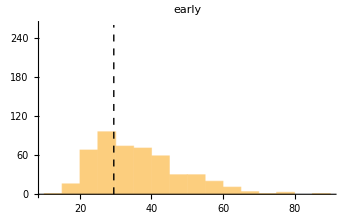
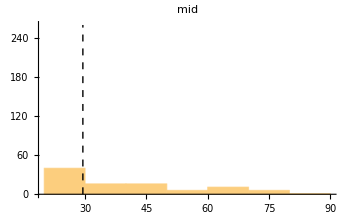
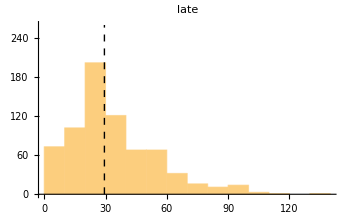
-Graphics--Graphics--Graphics-GATA6 expression of ICM cells

```mathematica
Labeled[Row[Table[Show[Histogram[exprGata6ICMByStage[[i]],PlotLabel->{"early","mid","late"}[[i]],ImageSize->350,PlotRange->All],Graphics[{Black,Dashed,Line[{{gata6LineIni[[1]],0},{gata6LineIni[[1]],260}}]}]],{i,1,3}]],Style["GATA6 expression of ICM cells",FontFamily->fontOption,14],Top]
```

#### Underlying data TE cells

find TE cells that are neighbours of ICM cells and get their expression values for NANOG and GATA6

```mathematica
nanogNanogComp=compareValPopCentroidNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogNanogCompICM=Table[{nanogNanogComp[[i,1]], Select[nanogNanogComp[[i,2]],#[[1,1]]≠"TE"&]},{i,1,Length[nanogNanogComp]}];
```

```mathematica
centroidsTENeighbours=Select[DeleteDuplicates[Flatten[nanogNanogCompICM[[All,2,All,2]],2]],#[[2]]=="TE"&][[All,-1]];
```

```mathematica
nucleiFeaturesTE=Table[Select[i,("TE/ICM"/.#)=="TE"&],{i,nucleiFeatures}];
```

```mathematica
cellValuesTE=Transpose[{staging,nucleiFeaturesTE}];
```

```mathematica
cellValuesTEByNCBStage=Table[Select[cellValuesTE,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

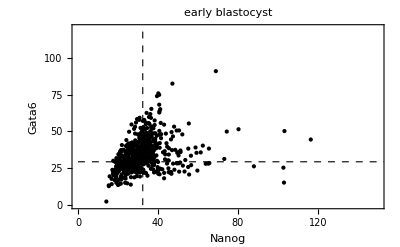
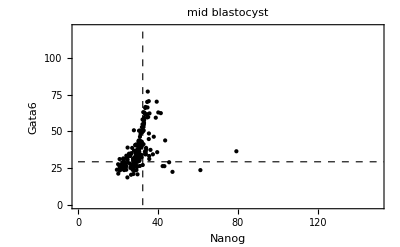
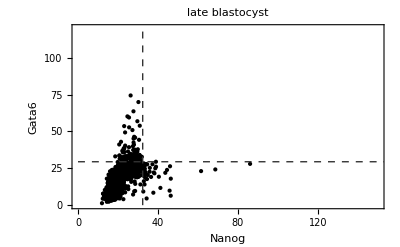
-Graphics--Graphics--Graphics-TE cells

```mathematica
Labeled[
Row[Table[Show[Graphics[{Black,PointSize->0.008,Point/@({"Nanog-AvgShifted","Gata6-AvgShifted"}/.#[[2]])}&/@cellValuesTEByNCBStage[[i]],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"},AspectRatio->1/GoldenRatio],Graphics[{GrayLevel[0.2],Dashed,Line[{{0,gata6LineIni[[1]]},{200,gata6LineIni[[1]]}}],Line[{{nanogLineIni[[1]],0},{nanogLineIni[[1]],150.}}]}]],{i,1,3}],"      "],Style[#,FontFamily->"Arial"]&@"TE cells",Top]
```

```mathematica
nucleiFeaturesTENeighbours=Table[Select[i,MemberQ[centroidsTENeighbours,("Centroid"/.#)]==True&],{i,nucleiFeaturesTE}];
```

```mathematica
cellValuesTENeighbours=Transpose[{staging,nucleiFeaturesTENeighbours}];
```

```mathematica
cellValuesTENeighByNCBStage=Table[Select[cellValuesTENeighbours,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

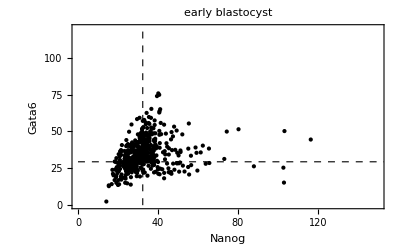
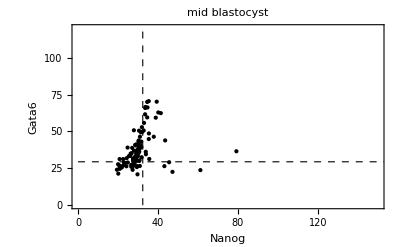
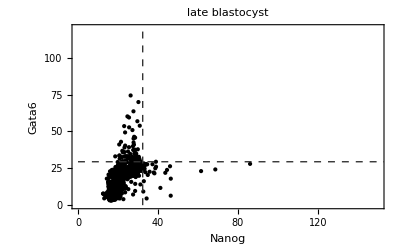
-Graphics--Graphics--Graphics-TE cells that are neighbours of ICM cells

```mathematica
Labeled[
Row[Table[Show[Graphics[{Black,PointSize->0.008,Point/@({"Nanog-AvgShifted","Gata6-AvgShifted"}/.#[[2]])}&/@cellValuesTENeighByNCBStage[[i]],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"},AspectRatio->1/GoldenRatio],Graphics[{GrayLevel[0.2],Dashed,Line[{{0,gata6LineIni[[1]]},{200,gata6LineIni[[1]]}}],Line[{{nanogLineIni[[1]],0},{nanogLineIni[[1]],150.}}]}]],{i,1,3}],"      "],Style[#,FontFamily->"Arial"]&@"TE cells that are neighbours of ICM cells",Top]
```

```mathematica
exprTENeighbours=Flatten[{"TE/ICM","Nanog-AvgShifted","Gata6-AvgShifted"}/.nucleiFeaturesTENeighbours,1];
```

```mathematica
nanogValuesTENeighbours=exprTENeighbours[[All,2]];
```

```mathematica
gata6ValuesTENeighbours=exprTENeighbours[[All,3]];
```

```mathematica
Mean[nanogValuesTENeighbours]
```

27.3459

```mathematica
Mean[gata6ValuesTENeighbours]
```

26.2554

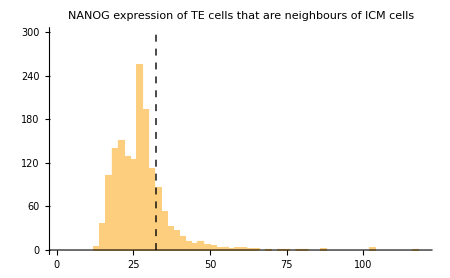
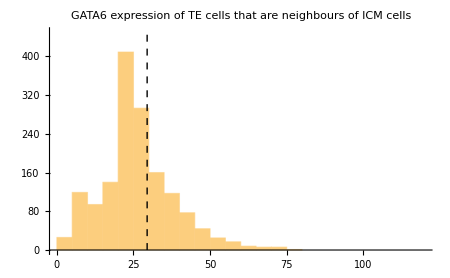

```mathematica
Row[{Show[Histogram[nanogValuesTENeighbours,PlotLabel->"NANOG expression of TE cells that are neighbours of ICM cells",ImageSize->450,PlotRange->{{0,120},All}],Graphics[{Black,Dashed,Line[{{nanogLineIni[[1]],0},{nanogLineIni[[1]],300}}]}]],Show[Histogram[gata6ValuesTENeighbours,PlotLabel->"GATA6 expression of TE cells that are neighbours of ICM cells",PlotRange->{{0,120},All},ImageSize->450],Graphics[{Black,Dashed,Line[{{gata6LineIni[[1]],0},{gata6LineIni[[1]],450}}]}]]},"    "]
```

### Populations count (Fig S2 B and C)

```mathematica
cellValuesTENeigh=Transpose[{staging,nucleiFeaturesTENeighbours}];
```

```mathematica
populationsCountTENeigh=Table[{cellValuesTENeigh[[i,1,1]],cellValuesTENeigh[[i,1,2]],cellValuesTENeigh[[i,1,3]],Count["Quadrant"/.cellValuesTENeigh[[i,2]],#]&/@{"N-G-","N+G+","N+G-","N-G+"}},{i,1,Length[cellValuesTENeigh]}];
```

```mathematica
populationsCountByStageTENeigh=Table[Select[populationsCountTENeigh,#[[3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountAllTENeighByStage=Table[Total@populationsCountByStageTENeigh[[i,All,-1]],{i,1,3}]
```

{{129,176,47,157},{28,21,4,54},{824,0,27,75}}

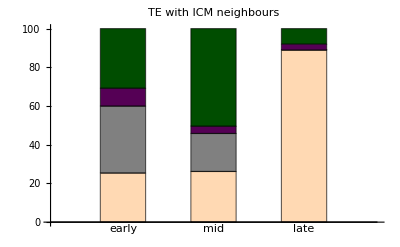

```mathematica
Labeled[BarChart[popCountAllTENeighByStage,BarSpacing->1,ChartLayout->"Percentile",ImageSize->400,ChartStyle->{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},ChartLabels->{{"early","mid","late"},None},PlotLabel->"TE with ICM neighbours"], SwatchLegend[{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},{"DN","DP","Epi progenitor","PrE progenitor"},LegendLayout->"Row"]]
```

```mathematica
cellValuesTE=Transpose[{staging,nucleiFeaturesTE}];
```

```mathematica
populationsCountTE=Table[{cellValuesTE[[i,1,1]],cellValuesTE[[i,1,2]],cellValuesTE[[i,1,3]],Count["Quadrant"/.cellValuesTE[[i,2]],#]&/@{"N-G-","N+G+","N+G-","N-G+"}},{i,1,Length[cellValuesTE]}];
```

```mathematica
populationsCountByStageTE=Table[Select[populationsCountTE,#[[3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountAllTEByStage=Table[Total@populationsCountByStageTE[[i,All,-1]],{i,1,3}]
```

{{160,205,54,220},{62,41,6,97},{1474,0,42,101}}

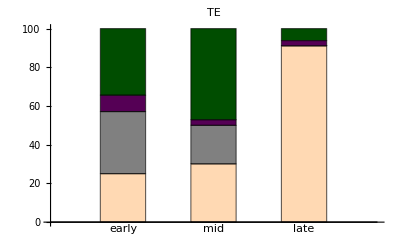

```mathematica
Labeled[BarChart[popCountAllTEByStage,BarSpacing->1,ChartLayout->"Percentile",ImageSize->400,ChartStyle->{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},ChartLabels->{{"early","mid","late"},None},PlotLabel->"TE"], SwatchLegend[{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},{"DN","DP","Epi progenitor","PrE progenitor"},LegendLayout->"Row"]]
```

### Null models for correlations (see Sup. Info)

random values are assigned to ICM cells in an embryo, TE cells keep their original value
correlations are calculated considering ICM cells and their neighbours

#### Functions for drawing random values

```mathematica
randomExprNanogData[nucleiFeatures_,modus_:{"draw","sample","shuffle","sampleByStage","uniform"}[[1]],stage_:"NA"]:=Block[{exprSim,j,exprThisEmbryo,index,sampleSize},
exprSim=Switch[modus, "draw", 
RandomChoice[exprNanogICM,Length[nucleiFeatures]],
 "sample", 
RandomSample[exprNanogICM,Length[nucleiFeatures]],
"shuffle",
(exprThisEmbryo=Select[{"TE/ICM","Nanog-AvgShifted"}/.nucleiFeatures,#[[1]]≠"TE"&][[All,2]];
RandomSample[exprThisEmbryo,Length[exprThisEmbryo]]),
"sampleByStage",
(index=stage/.{3.5->1,4.0->2,4.5->3};
sampleSize=Length[nucleiFeatures]-Count["TE/ICM"/.nucleiFeatures,"TE"];
RandomSample[exprNanogICMByStage[[index]],sampleSize]),
"uniform",
RandomReal[{0,1},Length[nucleiFeatures]]];
j=1;
If [("TE/ICM"/.#)=="ICM+Epi",#/.Rule["Nanog-AvgShifted",_]->Rule["Nanog-AvgShifted",exprSim[[j++]]],#]&/@nucleiFeatures
]
```

```mathematica
randomExprGata6Data[nucleiFeatures_,modus_:{"draw","sample","shuffle","sampleByStage","uniform"}[[1]],stage_:"NA"]:=Block[{exprSim,j,exprThisEmbryo,index,sampleSize},
exprSim=Switch[modus, "draw", 
RandomChoice[exprGata6ICM,Length[nucleiFeatures]],
 "sample", 
RandomSample[exprGata6ICM,Length[nucleiFeatures]],
"shuffle",
(exprThisEmbryo=Select[{"TE/ICM","Gata6-AvgShifted"}/.nucleiFeatures,#[[1]]≠"TE"&][[All,2]];
RandomSample[exprThisEmbryo,Length[exprThisEmbryo]]),
"sampleByStage",
(index=stage/.{3.5->1,4.0->2,4.5->3};
sampleSize=Length[nucleiFeatures]-Count["TE/ICM"/.nucleiFeatures,"TE"];
RandomSample[exprGata6ICMByStage[[index]],sampleSize]),
"uniform",
RandomReal[{0,1},Length[nucleiFeatures]]];
j=1;
If [("TE/ICM"/.#)=="ICM+Epi",#/.Rule["Gata6-AvgShifted",_]->Rule["Gata6-AvgShifted",exprSim[[j++]]],#]&/@nucleiFeatures
]
```

```mathematica
randomCorrAnaDataByStages[nucleiFeatures_,marker_,dcgGraphs_,corrMode_:{"all","ICM"}[[1]],modus_:{"draw","sample","shuffle","sampleByStage","uniform"}[[1]],stage_:{}]:=Block[{randomFeatures,randomComp,randomCompRaw,randomCompByStages,cellValues},
cellValues=If[Length[stage]==Length[nucleiFeatures],
Transpose[{stage[[All,3]],nucleiFeatures}],
{"NA",#}&/@nucleiFeatures];
randomFeatures=Switch[marker,"Nanog",randomExprNanogData[#[[2]],modus,#[[1]]]&/@cellValues,"Gata6",randomExprGata6Data[#[[2]],modus,#[[1]]]&/@cellValues];
randomComp=Switch[corrMode,"all",
compareValNeighboursFun[randomFeatures,dcgGraphs,StringJoin[marker,"-AvgShifted"],StringJoin[marker,"-AvgShifted"]],
"ICM",
(randomCompRaw=compareValNeighboursFun[randomFeatures,dcgGraphs,StringJoin[marker,"-AvgShifted"],StringJoin[marker,"-AvgShifted"]];
Table[{randomCompRaw[[i,1]], Select[randomCompRaw[[i,2]],#[[1,1]]≠"TE"&]},{i,1,Length[randomCompRaw]}])
];
randomCompByStages={Select[randomComp,#[[1,3]]==3.5&],Select[randomComp,#[[1,3]]==4.0&],Select[randomComp,#[[1,3]]==4.5&]};
{
"correlationsByStages"->Table[Correlation[#[[All,1,2]]&@Flatten[randomCompByStages[[i,All,2]],1],Median[#[[2]]]&/@Flatten[randomCompByStages[[i,All,2]],1]],{i,1,3}]}
]
```

```mathematica
randomCorrAnaTwoMarkersByStages[nucleiFeatures_,marker_,markerNeigh_,dcgGraphs_,corrMode_:{"all","ICM"}[[1]]]:=Block[{randomFeaturesFirst,randomFeatures,randomComp,randomCompRaw,randomCompByEVStages,randomCompByNCBStages,cellValues},
randomFeaturesFirst=randomExprNanogData/@nucleiFeatures;
randomFeatures=randomExprGata6Data/@randomFeaturesFirst;
randomComp=Switch[corrMode,"all",
compareValNeighboursFun[randomFeatures,dcgGraphs,StringJoin[marker,"-AvgShifted"],StringJoin[markerNeigh,"-AvgShifted"]],
"ICM",
(randomCompRaw=compareValNeighboursFun[randomFeatures,dcgGraphs,StringJoin[marker,"-AvgShifted"],StringJoin[markerNeigh,"-AvgShifted"]];
Table[{randomCompRaw[[i,1]], Select[randomCompRaw[[i,2]],#[[1,1]]≠"TE"&]},{i,1,Length[randomCompRaw]}])
];
randomCompByNCBStages={Select[randomComp,#[[1,2]]=="3.5ncb"&],Select[randomComp,#[[1,2]]=="4.0ncb"&],Select[randomComp,#[[1,2]]=="4.5ncb"&]};
{
"correlationsByNCBStages"->Table[Correlation[#[[All,1,2]]&@Flatten[randomCompByNCBStages[[i,All,2]],1],Median[#[[2]]]&/@Flatten[randomCompByNCBStages[[i,All,2]],1]],{i,1,3}]}
]
```

```mathematica
shuffleByStage[nucleiFeatures_,staging_,dcgGraphs_,marker_,corrMode_:{"all","ICM"}[[1]]]:=Block[{nucleiFeaturesID,cellValues,cellValuesByStage,dcgGraphsByStage,randomFeatures,randomComp,randomCompRaw,randomCompICMByNCBStages},
nucleiFeaturesID=Table[nucleiFeatures[[i]]/.Rule["EmbryoId",_]->Rule["EmbryoId",staging[[i,2]]],{i,1,Length[nucleiFeatures]}];
cellValues=Transpose[{staging,nucleiFeaturesID}];
cellValuesByStage=Table[Select[cellValues,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
dcgGraphsByStage=Table[Select[dcgGraphs,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
randomFeatures=Switch[marker,"Nanog",
Table[SplitBy[randomExprNanogData[Flatten[cellValuesByStage[[i,All,2]],1],"sampleByStage",{3.5,4.0,4.5}[[i]]],"EmbryoId"/.#&],{i,1,3}],
"Gata6",
Table[SplitBy[randomExprGata6Data[Flatten[cellValuesByStage[[i,All,2]],1],"sampleByStage",{3.5,4.0,4.5}[[i]]],"EmbryoId"/.#&],{i,1,3}]];
randomComp=Switch[corrMode,"all",
compareValNeighboursFun[Flatten[randomFeatures,1],Flatten[dcgGraphsByStage,1],StringJoin[marker,"-AvgShifted"],StringJoin[marker,"-AvgShifted"]],
"ICM",
(randomCompRaw=compareValNeighboursFun[Flatten[randomFeatures,1],Flatten[dcgGraphsByStage,1],StringJoin[marker,"-AvgShifted"],StringJoin[marker,"-AvgShifted"]];
Table[{randomCompRaw[[i,1]], Select[randomCompRaw[[i,2]],#[[1,1]]≠"TE"&]},{i,1,Length[randomCompRaw]}])
];
randomCompICMByNCBStages=Table[Select[randomComp,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
{"correlationsByNCBStages"->Table[Correlation[#[[All,1,2]]&@Flatten[randomCompICMByNCBStages[[i,All,2]],1],Median[#[[2]]]&/@Flatten[randomCompICMByNCBStages[[i,All,2]],1]],{i,1,3}]}
]
```

#### Draw from uniform distribution ICM, correlations for ICM cells (Sup. Info: Random model 1)

generate and save random numbers

```mathematica
DistributeDefinitions[#]&/@{randomExprNanogData,randomExprGata6Data,exprNanogICM,exprGata6ICM,randomCorrAnaDataByStages,compareValNeighboursFun};
```

```mathematica
resUniform01=ParallelTable[randomCorrAnaDataByStages[nucleiFeatures,"Nanog",dcgGraphs,"ICM","uniform"],{i,1,100}];
```

$Aborted

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","uniformICMByStagesTEOrg.mx"}],resUniform01];
```

evaluate random numbers

```mathematica
resUniform01=Import[FileNameJoin[{NotebookDirectory[],"Results","uniformICMByStagesTEOrg.mx"}]];
```

```mathematica
parUniform01ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resUniform01])
```

{{-0.000626192,0.0422242},{0.146027,0.0106396},{0.250353,0.0027867}}

numbers in paper

```mathematica
resUniform01=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","uniformICMByStagesTEOrg.mx"}]];
```

```mathematica
parUniform01ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resUniform01])
```

{{-0.000626192,0.0422242},{0.146027,0.0106396},{0.250353,0.0027867}}

#### Shuffeling values in ICM, correlations for ICM cells (Sup. Info: Random model 2)

generate and save random numbers

```mathematica
DistributeDefinitions[#]&/@{randomExprNanogData,randomExprGata6Data,exprNanogICM,exprGata6ICM,randomCorrAnaDataByStages,compareValNeighboursFun};
```

{{},{},{},{},{},{}}

```mathematica
resNanog=ParallelTable[randomCorrAnaDataByStages[nucleiFeatures,"Nanog",dcgGraphs,"ICM","shuffle"],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","shuffleNanogICMByStagesTEOrg.mx"}],resNanog];
```

```mathematica
resGata6=ParallelTable[randomCorrAnaDataByStages[nucleiFeatures,"Gata6",dcgGraphs,"ICM","shuffle"],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","shuffleGata6ICMByStagesTEOrg.mx"}],resGata6]
```

evaluate random numbers

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results","shuffleNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","shuffleGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resNanog])
```

{{0.194558,0.0412628},{0.0385507,0.0806879},{0.293165,0.0503075}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resGata6])
```

{{0.635644,0.0135964},{0.390057,0.0659074},{0.377631,0.0399987}}

numbers in paper

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","shuffleNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","shuffleGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resNanog])
```

{{0.194558,0.0412628},{0.0385507,0.0806879},{0.293165,0.0503075}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resGata6])
```

{{0.635644,0.0135964},{0.390057,0.0659074},{0.377631,0.0399987}}

#### Drawing randomly from the two distributions, correlations for ICM cells (Sup. Info: Random model 3)

random values are taken from the distributions of levels of NANOG and GATA6 in ICM cells of all embryos

generate and save random numbers

```mathematica
DistributeDefinitions[randomCorrAnaDataByStages,compareValNeighboursFun,randomExprGata6Data,randomExprNanogData];
```

{}

```mathematica
resNanog=ParallelTable[randomCorrAnaDataByStages[nucleiFeatures,"Nanog",dcgGraphs,"ICM","draw"],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","randomExprNanogICMByStagesTEOrg.mx"}],resNanog];
```

```mathematica
resGata6=ParallelTable[randomCorrAnaDataByStages[nucleiFeatures,"Gata6",dcgGraphs,"ICM","draw"],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","randomExprGata6ICMByStagesTEOrg.mx"}],resGata6]
```

R:\users\sschambe\Silvia\embryoAnalysis\paperCellNum\Results\randomExprGata6ICMByNCBStagesTEOrg.mx

evaluate random numbers

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results","randomExprNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","randomExprGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByStages"/.#&/@resNanog])
```

{{-0.00500032,0.045301},{-0.0170973,0.107791},{0.00384738,0.0364605}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByStages"/.#&/@resGata6])
```

{{-0.0052612,0.0535947},{0.000312176,0.104969},{-0.000109078,0.0412517}}

numbers in paper

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","randomExprNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","randomExprGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resNanog])
```

{{-0.00500032,0.045301},{-0.0170973,0.107791},{0.00384738,0.0364605}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resGata6])
```

{{-0.0052612,0.0535947},{0.000312176,0.104969},{-0.000109078,0.0412517}}

#### Sample randomly by stage, correlations for ICM cells (Sup. Info: Random model 4)

generate and save random numbers

```mathematica
DistributeDefinitions[#]&@{randomExprNanogData,randomExprGata6Data,exprNanogICM,exprGata6ICM,exprNanogICMByStage,exprGata6ICMByStage,randomCorrAnaDataByStages,compareValNeighboursFun};
```

{}

```mathematica
Length[nucleiFeatures]
```

44

```mathematica
resNanog=ParallelTable[randomCorrAnaDataByStages[nucleiFeatures,"Nanog",dcgGraphs,"ICM","sampleByStage",staging],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","sampleByStageNanogICMByNCBStagesTEOrg.mx"}],resNanog];
```

```mathematica
resGata6=ParallelTable[randomCorrAnaDataByStages[nucleiFeatures,"Gata6",dcgGraphs,"ICM","sampleByStage",staging],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","sampleByStageExprGata6ICMByStagesTEOrg.mx"}],resGata6]
```

R:\users\sschambe\Silvia\embryoAnalysis\paperCellNum\Results\sampleByStageExprGata6ICMByNCBStagesTEOrg.mx

evaluate random numbers

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results","sampleByStageNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","sampleByStageExprGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByStages"/.#&/@resNanog])
```

{{-0.00881659,0.0429659},{-0.0226294,0.0993326},{-0.0157581,0.0391274}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByStages"/.#&/@resGata6])
```

{{-0.00143943,0.0496067},{-0.021951,0.104114},{0.00178558,0.0414802}}

numbers in paper

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","sampleByStageNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","sampleByStageExprGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resNanog])
```

{{-0.00881659,0.0429659},{-0.0226294,0.0993326},{-0.0157581,0.0391274}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resGata6])
```

{{-0.00143943,0.0496067},{-0.021951,0.104114},{0.00178558,0.0414802}}

#### Shuffle by stage, correlations for all ICM cells (Sup. Info: Random model 5)

generate and save random numbers

```mathematica
DistributeDefinitions[#]&@{shuffleByStage,randomExprNanogData,randomExprGata6Data,exprNanogICM,exprGata6ICM,exprNanogICMByStage,exprGata6ICMByStage,randomCorrAnaDataByStages,compareValNeighboursFun};
```

{}

```mathematica
resNanog=ParallelTable[shuffleByStage[nucleiFeatures,staging,dcgGraphs,"Nanog","ICM"],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","shuffleByStageNanogICMByStagesTEOrg.mx"}],resNanog];
```

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results\\shuffleByStageNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=ParallelTable[shuffleByStage[nucleiFeatures,staging,dcgGraphs,"Gata6","ICM"],{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","shuffleByStageExprGata6ICMByStagesTEOrg.mx"}],resGata6]
```

R:\users\sschambe\Silvia\embryoAnalysis\paperCellNum\Results\shuffleByStageExprGata6ICMByNCBStagesTEOrg.mx

evaluate random numbers

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results\\shuffleByStageNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","shuffleByStageExprGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resNanog])
```

{{0.00252256,0.0558797},{0.0020325,0.120522},{-0.00998802,0.039319}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resGata6])
```

{{-0.00350265,0.051448},{0.00437491,0.1184},{0.00602293,0.0437573}}

numbers in paper

```mathematica
resNanog=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","shuffleByStageNanogICMByStagesTEOrg.mx"}]];
```

```mathematica
resGata6=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","shuffleByStageExprGata6ICMByStagesTEOrg.mx"}]];
```

```mathematica
parNanogByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resNanog])
```

{{0.00252256,0.0558797},{0.0020325,0.120522},{-0.00998802,0.039319}}

```mathematica
parGata6ByStages=Through[{Mean,StandardDeviation}[#]]&/@(Transpose["correlationsByNCBStages"/.#&/@resGata6])
```

{{-0.00350265,0.051448},{0.00437491,0.1184},{0.00602293,0.0437573}}

## Number of neighbours in ICM by population type (Fig S3 B)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
cellValues=Transpose[{staging,nucleiFeatures}];
```

```mathematica
cellValuesICM={#[[1]],Select[#[[2]],("TE/ICM"/.#)!="TE"&]}&/@cellValues;
```

```mathematica
popNumNeighICM={#[[1,3]],{"Quadrant","DCGNeighborCount"}/.#[[2]]}&/@cellValuesICM;
```

```mathematica
popNumNeighICMByStages=Table[Select[popNumNeighICM,#[[1]]==j&],{j,{3.5,4.0,4.5}}];
```

```mathematica
numNeighICMByPopByStagesChart=Table[Table[{j,Select[Flatten[popNumNeighICMByStages[[i,All,2]],1],#[[1]]==j&][[All,2]]},{j,{"N-G-","N+G+","N+G-","N-G+"}}],{i,1,3}];
```

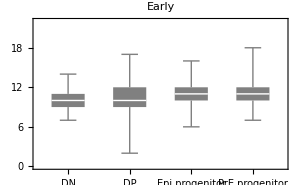
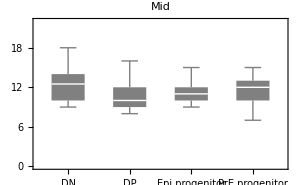
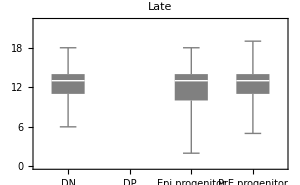

```mathematica
neighboursICMByPopType=Row[Table[BoxWhiskerChart[numNeighICMByPopByStagesChart[[i,All,2]],ChartStyle->Gray,FrameStyle->Directive[16,Black],PlotLabel->Style[{"Early","Mid","Late"}[[i]],Black,16],ChartLabels->(Rotate[#,45°]&/@{"DN","DP","Epi progenitor","PrE progenitor"}),ImageSize->300,PlotRange->{0,22}],{i,1,3}],"   "]
```

## Illustration of correlation number of neighbours and NANOG for ICM (Fig S6)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
earlyIndex=Position[staging,3.5][[All,1]]
```

{1,2,3,4,5,6,10,13,17,22,23,24,25,26,28,29,30,32,33,34,35,39,43,44}

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&], {i,1, Length[nucleiFeatures]}];
```

```mathematica
illNumNeighNanogEarlyI=Grid[Partition[Flatten@Table[{Graphics3D[{{ColorData["Rainbow"][1-(Abs[("DCGNeighborCount"/.#)-9]/Max[Abs[("DCGNeighborCount"/.nucleiFeaturesICM[[i]])-9]])],Sphere["Centroid"/.#,5]}&/@nucleiFeaturesICM[[i]]},Axes->True,AxesStyle->Directive[Black,24],AxesLabel->{"x","y","z"},PlotLabel->Style["Difference to\n nine neighbours",Directive[24,Black,fontOption]],ImageSize->300],Graphics3D[{{ColorData["Rainbow"][("Nanog-Avg"/.#)/Max["Nanog-Avg"/.nucleiFeaturesICM[[i]]]],Sphere["Centroid"/.#,5]}&/@nucleiFeaturesICM[[i]]},Axes->True,AxesStyle->Directive[Black,24],AxesLabel->{"x","y","z"},PlotLabel->Style["NANOG",Directive[24,Black,fontOption]],ImageSize->300]},{i,earlyIndex[[1;;12]]}],4],Dividers->{{{True,False}},All},Spacings->{2,2}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
illNumNeighNanogEarlyII=Grid[Partition[Flatten@Table[{Graphics3D[{{ColorData["Rainbow"][1-(Abs[("DCGNeighborCount"/.#)-9]/Max[Abs[("DCGNeighborCount"/.nucleiFeaturesICM[[i]])-9]])],Sphere["Centroid"/.#,5]}&/@nucleiFeaturesICM[[i]]},Axes->True,AxesStyle->Directive[Black,24],AxesLabel->{"x","y","z"},PlotLabel->Style["Difference to\n nine neighbours",Directive[24,Black,fontOption]],ImageSize->300],Graphics3D[{{ColorData["Rainbow"][("Nanog-Avg"/.#)/Max["Nanog-Avg"/.nucleiFeaturesICM[[i]]]],Sphere["Centroid"/.#,5]}&/@nucleiFeaturesICM[[i]]},Axes->True,AxesStyle->Directive[Black,24],AxesLabel->{"x","y","z"},PlotLabel->Style["NANOG",Directive[24,Black,fontOption]],ImageSize->300]},{i,earlyIndex[[11;;-1]]}],4],Dividers->{{{True,False}},All},Spacings->{2,2}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
BarLegend["Rainbow",LabelStyle->White]
```

## Null Models: expression versus number of neighbours and expression vs distance from centroid (Fig S7)

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

#### Underlying data ICM cells

```mathematica
nucleiFeaturesICM=Select[#,("TE/ICM"/.#)≠"TE"&]&/@nucleiFeatures;
```

```mathematica
exprNanogICM=Select[Flatten[{"TE/ICM","Nanog-AvgShifted"}/.nucleiFeaturesICM,1],#[[2]]>0&][[All,2]];
```

```mathematica
Mean[exprNanogICM]
```

42.0196

```mathematica
exprGata6ICM=Select[Flatten[{"TE/ICM","Gata6-AvgShifted"}/.nucleiFeaturesICM,1],#[[2]]>0&][[All,2]];
```

```mathematica
Mean[exprGata6ICM]
```

35.0867

#### Functions for drawing random values

```mathematica
randomExprNanogData[nucleiFeatures_]:=If [("TE/ICM"/.#)=="ICM+Epi",#/.Rule["Nanog-AvgShifted",_]->Rule["Nanog-AvgShifted",RandomChoice[exprNanogICM]],#]&/@nucleiFeatures
```

```mathematica
randomExprGata6Data[nucleiFeatures_]:=If [("TE/ICM"/.#)=="ICM+Epi",#/.Rule["Gata6-AvgShifted",_]->Rule["Gata6-AvgShifted",RandomChoice[exprGata6ICM]],#]&/@nucleiFeatures
```

### Generate and save random expressions

```mathematica
randomFeatures=Table[randomFeaturesFirst=randomExprNanogData/@nucleiFeatures;
randomExprGata6Data/@randomFeaturesFirst,{i,1,100}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","RandomFeatures_"<>DateString["ISODate"]<>".mx"}],randomFeatures]
```

R:\users\sschambe\Silvia\embryoAnalysis\paperCellNum\Results\RandomFeatures_2019-02-04.mx

numbers in paper

```mathematica
randomFeatures=Import[FileNameJoin[{NotebookDirectory[],"Results","paper","RandomFeatures_2019-02-04.mx"}]];
```

### Expression vs number of neighbours (Fig S7 A)

#### NANOG

average all simulations per embryo

```mathematica
nanogNumNeighbours=
Table[Mean[{"TE/ICM","DCGNeighborCount","Nanog-AvgShifted"}/.randomFeatures[[All,i]]],{i,1,Length[randomFeatures[[1]]]}];
```

```mathematica
nanogNumNeighboursByStages={Select[nanogNumNeighbours,Length[#]<65&],Select[nanogNumNeighbours,(Length[#]>=65)&&(Length[#]≤90)&],Select[nanogNumNeighbours,Length[#]>90&]};
```

```mathematica
nanogNumNeighbByStagesAvgICMAll=Table[SortBy[{#[[1,1]],Mean[#[[All,2]]],If[Length[#]>1,StandardDeviation[#[[All,2]]]/Sqrt[Length[#]],0]}&/@GatherBy[Select[Flatten[nanogNumNeighboursByStages[[i]],1],#[[1]]≠"TE"&][[All,-2;;-1]],#[[1]]&],#[[1]]&],{i,1,3}];
```

remove those that are only for one cell, i.e. std dev =0

```mathematica
nanogNumNeighbByStagesAvgICMAllNS0=Select[#,#[[3]]≠0&]&/@nanogNumNeighbByStagesAvgICMAll;
```

for numNeighb 19, there are only two cells and the distribution of NANOG has a longer tail than for GATA6

```mathematica
nanogNumNeighbByStagesAvgICMAllNS0Smooth=smoothedValues[nanogNumNeighbByStagesAvgICMAllNS0,1];
```

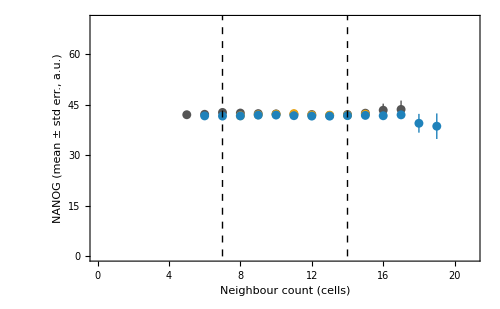

```mathematica
nullModelNeighNumNPoint=Show[ErrorListPlot[Table[{#[[1;;2]],ErrorBar[#[[3]]]}&/@nanogNumNeighbByStagesAvgICMAllNS0Smooth[[i]],{i,1,3}],PlotStyle->({Thick,colour3[#]}&/@{1,2,3}),PlotRange->{{0,21},{0,70}},AxesOrigin->{0,0},Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{"Neighbour count (cells)","NANOG (mean ± std err., a.u.)"},ImageSize->500,Joined->False],Graphics[{Black,Dashed,Line[{{7,0},{7,75}}],Line[{{14,0},{14,75}}]}]]
```

#### GATA6

```mathematica
gata6NumNeighbours=
Table[Mean[{"TE/ICM","DCGNeighborCount","Gata6-AvgShifted"}/.randomFeatures[[All,i]]],{i,1,Length[randomFeatures[[1]]]}];
```

```mathematica
gata6NumNeighboursByStages={Select[gata6NumNeighbours,Length[#]<65&],Select[gata6NumNeighbours,(Length[#]>=65)&&(Length[#]≤90)&],Select[gata6NumNeighbours,Length[#]>90&]};
```

```mathematica
gata6NumNeighbByStagesAvgICMAll=Table[SortBy[{#[[1,1]],Mean[#[[All,2]]],If[Length[#]>1,StandardDeviation[#[[All,2]]]/Sqrt[Length[#]],0]}&/@GatherBy[Select[Flatten[gata6NumNeighboursByStages[[i]],1],#[[1]]≠"TE"&][[All,-2;;-1]],#[[1]]&],#[[1]]&],{i,1,3}];
```

remove those that are only for one cell, i.e. std dev =0

```mathematica
gata6NumNeighbByStagesAvgICMAllNS0=Select[#,#[[3]]≠0&]&/@gata6NumNeighbByStagesAvgICMAll;
```

```mathematica
gata6NumNeighbByStagesAvgICMAllNS0Smooth=smoothedValues[gata6NumNeighbByStagesAvgICMAllNS0,1];
```

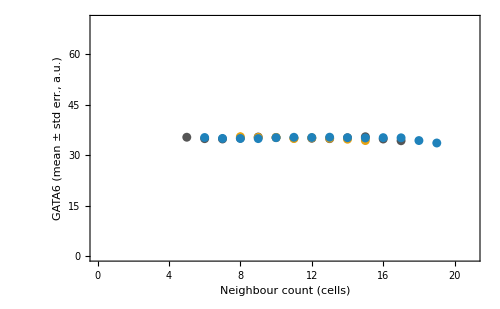

```mathematica
nullModelNeighNumGPoint=ErrorListPlot[Table[{#[[1;;2]],ErrorBar[#[[3]]]}&/@gata6NumNeighbByStagesAvgICMAllNS0Smooth[[i]],{i,1,3}],PlotStyle->({Thick,colour3[#]}&/@{1,2,3}),PlotRange->{{0,21},{0,70}},AxesOrigin->{0,0},Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{"Neighbour count (cells)","GATA6 (mean ± std err., a.u.)"},ImageSize->500,Joined->False]
```

### Expression vs distance from centroid (Fig S7 B)

```mathematica
randomFeaturesICM=Table[Select[#,("TE/ICM"/.#)!="TE"&]&/@randomFeatures[[j]],{j,1,100}];
```

```mathematica
stagingFun[numCells_]:=Switch[numCells,x_/;x<65,3.5,x_/;x<=90,4.0,x_/;x>90,4.5]
```

```mathematica
staging=stagingFun[Length[#]]&/@randomFeatures[[1]];
```

```mathematica
posExpr=Table[{staging[[i]],MapThread[Join,{({"Centroid"}/.randomFeaturesICM[[1,i]]),Mean[{"Nanog-AvgShifted","Gata6-AvgShifted"}/.randomFeaturesICM[[All,i]]]}]},{i,1,Length[staging]}];
```

calculate distance of cell to ICM centroid

```mathematica
distExprByStages=Table[Select[Table[{posExpr[[i,1]],{EuclideanDistance[#[[1]],Mean[#[[All,1]]]&@posExpr[[i,2]]],#[[2]],#[[3]]}&/@posExpr[[i,2]]},{i,1,Length[posExpr]}],#[[1]]==j&],{j,{3.5,4.0,4.5}}];
```

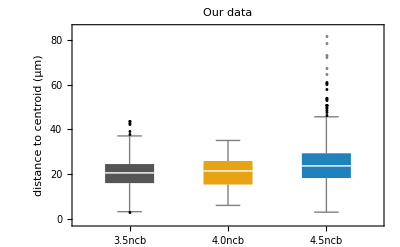

```mathematica
BoxWhiskerChart[Table[Flatten[distExprByStages[[i,All,2]],1][[All,1]],{i,1,3}],"Outliers",ChartLabels->{"3.5ncb","4.0ncb","4.5ncb"},FrameLabel->{None,"distance to centroid (µm)",None,None},FrameStyle->Directive[Black,16,FontFamily->"Arial"],ChartStyle->(colour3/@{1,2,3}),PlotLabel->Style["Our data",Black,16,FontFamily->"Arial"]]
```

```mathematica
avgRadius=Median[Flatten[Table[Max[#[[All,1]]]&/@distExprByStages[[i,All,2]],{i,1,3}]]]
```

34.3987

```mathematica
avgDistNanogByStages=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[#[[1;;2]]&/@Flatten[distExprByStages[[i,All,2]],1],{0,65,5},{0,10^6,10^6}],1],Length[#]>0&]),{i,1,3}];
```

use only those for more than one cell, hence std dev is not 0

```mathematica
avgDistNanogByStagesNoS0=Select[#,#[[3]]!=0&]&/@avgDistNanogByStages;
```

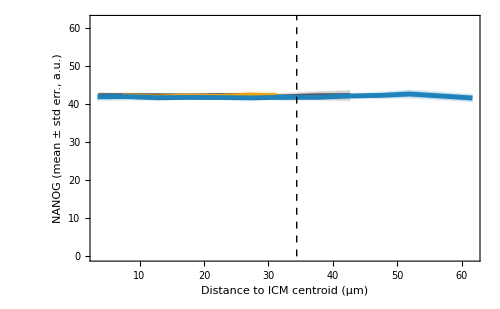

```mathematica
plotDistCentNanog=Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistNanogByStagesNoS0,#[[All,2;;3]]&/@avgDistNanogByStagesNoS0,1,"Distance to ICM centroid (µm)","NANOG (mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,62},ImageSize->500]
```

```mathematica
avgDistGata6ByStages=Table[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[#[[{1,3}]]&/@Flatten[distExprByStages[[i,All,2]],1],{0,65,5},{0,10^6,10^6}],1],Length[#]>0&]),{i,1,3}];
```

```mathematica
avgDistGata6ByStagesNoS0=Select[#,#[[3]]!=0&]&/@avgDistGata6ByStages;
```

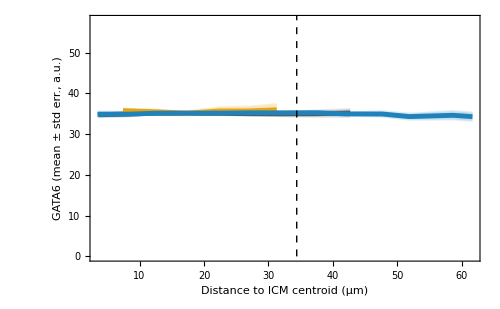

```mathematica
plotDistCentGata6=Show[{plotMeanStdLighter[#[[All,1]]&/@avgDistGata6ByStagesNoS0,#[[All,2;;3]]&/@avgDistGata6ByStagesNoS0,1,"Distance to ICM centroid (µm)","GATA6 (mean ± std err., a.u.)",colour3],Graphics[{Black,Dashed,Line[{{avgRadius,0},{avgRadius,420}}]}]},PlotRange->{0,58},ImageSize->500]
```